```mathematica
f[x]==2
```

f[x]==2

```mathematica
DiscreteAsymptotic[Prime[n],n->Infinity]
```

n Log[n]

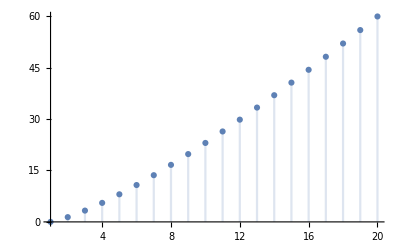

```mathematica
DiscretePlot[n Log[n],{n,1,20}]
```

```mathematica
DiscreteAsymptotic[Factorial[n],n->Infinity]
```

ⅇ^-n n^(1/2+n) √(2 π)

```mathematica
DiscretePlot[ⅇ^-n n^(1/2+n) √(2 π),{n,1,20}]
```

-Graphics-

```mathematica
DiscreteAsymptotic[Fibonacci[n],n->Infinity]
```

GoldenRatio^n/(√5)

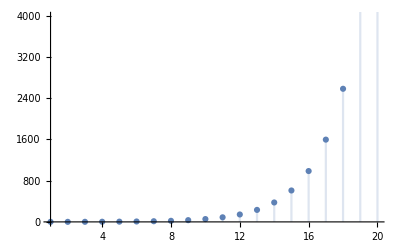

```mathematica
DiscretePlot[GoldenRatio^n/(√5),{n,1,20}]
```

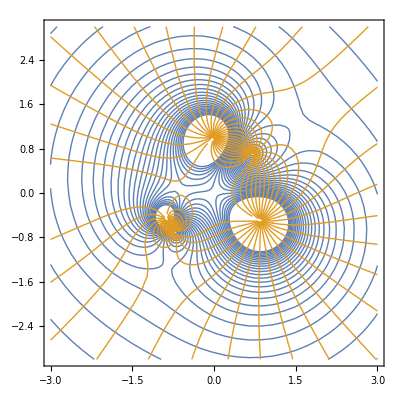

```mathematica
ComplexContourPlot[AbsArg[(z^2-I)/(z^3+I)],{z,-3-3 I,3+3 I},Contours->30]
```

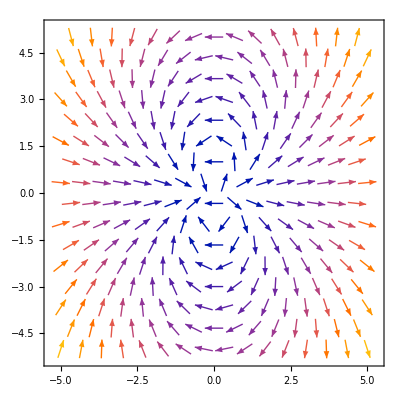

```mathematica
VectorPlot[{2 x^2-y^2,3 x y},{x,-5,5},{y,-5,5}]
```

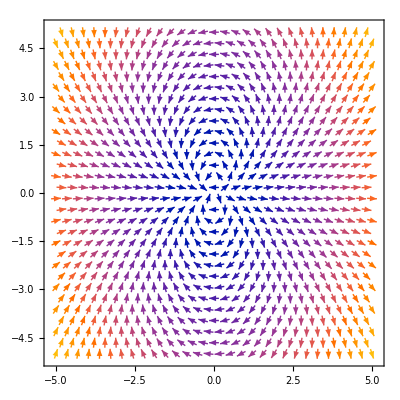

```mathematica
VectorPlot[{2 x^2-y^2,3 x y},{x,-5,5},{y,-5,5},VectorPoints->30]
```

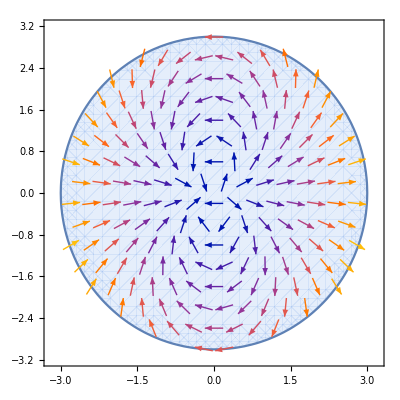

```mathematica
VectorPlot[{2 x^2-y^2,3 x y},{x,y}∈Disk[{0,0},3]]
```

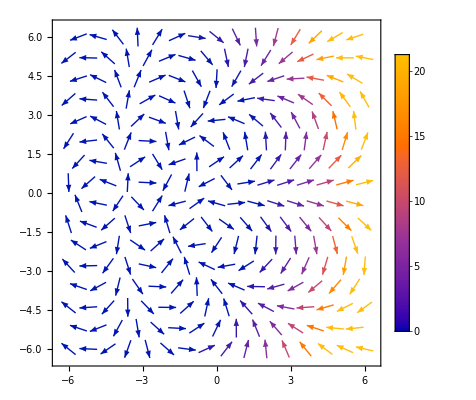

```mathematica
ComplexVectorPlot[z^Log[z],{z,6},PlotLegends->Automatic]
```

```mathematica
Graphics[Style[RegularPolygon[5],HatchFilling[]]]
```

-Graphics-

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,10},Filling->Axis,FillingStyle->HatchFilling[]]
```

-Graphics-

```mathematica
VideoFrameList[Video["ExampleData/Caminandes.mp4",Appearance->Automatic,AudioOutputDevice->Automatic,SoundVolume->Automatic],5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorCombine[%15,Automatic]
```

-Graphics-

```mathematica
Image3D[%15]
```

-Graphics3D-

```mathematica
ImageAssemble[%15]
```

-Graphics-

```mathematica
VideoTimeSeries[Mean,Video["ExampleData/Caminandes.mp4",Appearance->Automatic,AudioOutputDevice->Automatic,SoundVolume->Automatic]]
```

TimeSeries[…]

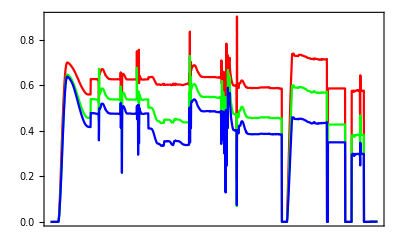

```mathematica
DateListPlot[%,PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]}]
```

```mathematica
Video["http://exampledata.wolfram.com/cars.avi"]
```

Video[http://exampledata.wolfram.com/cars.avi,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]http://exampledata.wolfram.com/cars.aviThumbnail1StandardForm

```mathematica
v=Video["http://exampledata.wolfram.com/cars.avi"]
```

Video[http://exampledata.wolfram.com/cars.avi,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]http://exampledata.wolfram.com/cars.aviThumbnail1StandardForm

```mathematica
ts=VideoTimeSeries[Point[ImagePosition[#,Entity["Word","car"]]]&,v]
```

TimeSeries[…]

```mathematica
HighlightImage[VideoExtractFrames[v,Quantity[5,"Seconds"]],{PointSize[Medium],Values[ts]}]
```

-Graphics-

```mathematica
Video[CloudGet["https://wolfr.am/L9r00rk5"]]
```

Video[C:\Users\sguzman\Documents\Wolfram\Video\6384e29a-ef87-4ab4-b2ae-92fda93d0796.mkv,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]C:\Users\sguzman\Documents\Wolfram\Video\6384e29a-ef87-4ab4-b2ae-92fda93d0796.mkvThumbnail1StandardForm

```mathematica
SpeechInterpreter["Airline"][CloudGet["https://wolfr.am/L9r410jA"]]
```

American Airlines Inc.

```mathematica
ds=CreateDataStructure["LinkedList"]
```

DataStructure[LinkedList, {Data -> {}}]

```mathematica
Do[ds["Append",RandomInteger[]],10^3]
```

```mathematica
ds["Visualization"]
```

-Graphics-

```mathematica
Mean[N[Normal[ds]]]
```

0.512

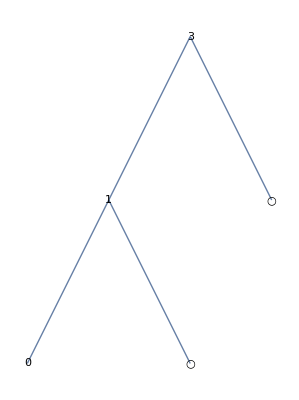

```mathematica
(ds=CreateDataStructure["BinaryTree",3->{1->{0,Null},Null}])["Visualization"]
```

```mathematica
RightRotate[y_]:=Module[{x,tmp},x=y["Left"];tmp=x["Right"];x["SetRight",y];
y["SetLeft",tmp];x]
```

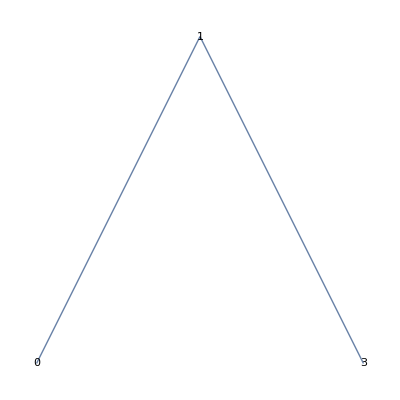

```mathematica
RightRotate[ds]["Visualization"]
```

```mathematica
InverseLaplaceTransform[1/(s Sqrt[s^3+1]),s,t]
```

InverseLaplaceTransform[1/(s √(1+s^3)),s,t]

```mathematica
Asymptotic[InverseLaplaceTransform[1/(s Sqrt[s^3+1]),s,t],t->0]
```

(4 t^(3/2))/(3 √π)

```mathematica
Asymptotic[DSolveValue[Sin[x]^2 y''[x]+x y[x]==0,y[x],x],{x,0,5}]
```

(x-x^2/2+x^3/12-(5 x^4)/144+(29 x^5)/2880) C[2]+C[1] ((1728+1728 x-2160 x^2+384 x^3-115 x^4)/1728+1/144 x (-144+72 x-12 x^2+5 x^3) Log[x])

```mathematica
DiscreteAsymptotic[Prime[n],n->Infinity]
```

n Log[n]

```mathematica
DiscreteAsymptotic[n!,n->Infinity]
```

ⅇ^-n n^(1/2+n) √(2 π)

```mathematica
DiscreteAsymptotic[n!,n->Infinity,SeriesTermGoal->5]
```

ⅇ^-n (1-571/(2488320 n^4)-139/(51840 n^3)+1/(288 n^2)+1/(12 n)) n^(1/2+n) √(2 π)

```mathematica
DiscreteAsymptotic[n!,n->Infinity,SeriesTermGoal->5]
```

ⅇ^-n (1-571/(2488320 n^4)-139/(51840 n^3)+1/(288 n^2)+1/(12 n)) n^(1/2+n) √(2 π)

```mathematica
DiscreteAsymptotic[BellB[n],n->Infinity]
```

(ⅇ^(-1-n+n/ProductLog[n]) (n/ProductLog[n])^(1/2+n))/(√n)

```mathematica
Series[HeunG[a,q,α,β,γ,δ,z],{z,0,3}]
```

1+(q z)/(a γ)-((α β+(q (-1-q-α-β+δ-a (γ+δ)))/(a γ)) z^2)/(2 (a (1+γ)))-(((q (1+α) (1+β))/(a γ)-((α β+(q (-1-q-α-β+δ-a (γ+δ)))/(a γ)) (-q-2 (2+α+β-δ+a (1+γ+δ))))/(2 a (1+γ))) z^3)/(3 (a (2+γ)))+O[z]^4

```mathematica
DSolveValue[(d+c x+b x^2) y[x]+a x y'[x]+(-1+x^2) y''[x]==0,y[x],x]
```

ⅇ^(√-b x) (-1/2+x/2)^(a/4) (1/2+x/2)^(1-a/4) (-1+x^2)^(-a/4) C[2] HeunC[1/4 a (-2+a-4 √-b)+4 √-b-b+c-d,2 (2 √-b+c),2-a/2,a/2,4 √-b,1/2+x/2]+ⅇ^(√-b x) ((-1+x) (1+x))^(a/4) (-1+x^2)^(-a/4) C[1] HeunC[a √-b-b+c-d,2 (a √-b+c),a/2,a/2,4 √-b,1/2+x/2]

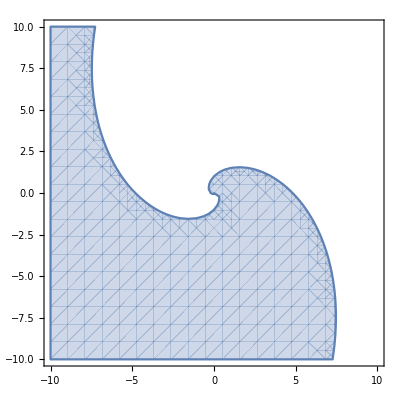

```mathematica
ComplexRegionPlot[Sqrt[z^(2+2 I)]==z^(1+I),{z,10}]
```

```mathematica
x^(α n)
```

x^(n α)

```mathematica
(x^2)^2
```

x^4

```mathematica
Composition[# #&, # #&]
```

#1 #1&@*(#1 #1&)

```mathematica
Composition[# #&, # #&][x]
```

x^4

```mathematica
Composition[# #&, # #&][Identity]
```

Identity^4

```mathematica
dist=CategoricalDistribution[{x,y,z},{.1,.2,.7}]
```

CategoricalDistribution[…]

```mathematica
RandomVariate[dist,10]
```

{y,z,z,z,z,z,x,z,z,z}

```mathematica
dist=CategoricalDistribution[{{"A","B","C"},{"D","E"},{"X","Y"}},{{{2,4},{2,1}},{{2,2},{3,2}},{{4,3},{1,3}}}]
```

CategoricalDistribution[…]

```mathematica
PDF[dist,{"A","D","Y"}]
```

4/29

```mathematica
Information[dist,"ProbabilityTable"]
```

```mathematica
cf=Classify[{1,2,3,4}->{a,a,b,b}]
```

ClassifierFunction[…]

```mathematica
cf[2.3]
```

a

```mathematica
cf[2.3,"Distribution"]
```

CategoricalDistribution[…]

```mathematica
Information[%,"ProbabilityTable"]
```

```mathematica
GeometricOptimization[π r (r+Sqrt[h^2+r^2]),{1≤π/3 h r^2},{h,r}]
```

{h→1.96948,r→0.696321}

```mathematica
GeometricOptimization[1/(h w d),{h≤2 w,d≤2 w,h*w+h*d≤50,2 w*d≤20},{h,w,d}]
```

{h→7.74594,w→3.87297,d→2.582}

```mathematica
With[{c1=0.25,c2=0.618},ineqs={{c1+w[1]+x[1]≤x[2],c1+w[1]+x[1]≤x[3],c1+w[1]+x[1]≤x[4],c1+w[1]+x[1]≤x[5],c1+w[1]+x[1]≤x[6],c1+w[1]+x[1]≤x[7],c1+w[2]+x[2]≤x[3],c1+w[4]+x[4]≤x[5],c1+w[2]+x[2]≤x[3],c1+w[2]+x[2]≤x[5],c1+w[2]+x[2]≤x[7],c1+w[4]+x[4]≤x[3],c1+w[4]+x[4]≤x[5],c1+w[4]+x[4]≤x[7],c1+w[6]+x[6]≤x[5],c1+w[8]+x[8]≤x[4],c1+w[9]+x[9]≤x[4],c1+w[10]+x[10]≤x[4],c1+w[10]+x[10]≤x[6],c1+w[6]+x[6]≤x[7],c1+w[8]+x[8]≤x[9],c1+w[8]+x[8]≤x[10],x[1]≥0,x[8]≥0,w[3]+x[3]≤𝓌,w[5]+x[5]≤𝓌,w[7]+x[7]≤𝓌},{c1+h[1]+y[1]≤y[6],c1+h[1]+y[1]≤y[7],c1+h[1]+y[1]≤y[8],c1+h[1]+y[1]≤y[9],c1+h[1]+y[1]≤y[10],c1+h[2]+y[2]≤y[4],c1+h[2]+y[2]≤y[9],c1+h[4]+y[4]≤y[6],c1+h[3]+y[3]≤y[5],c1+h[5]+y[5]≤y[7],c1+h[9]+y[9]≤y[6],c1+h[9]+y[9]≤y[10],y[1]≥0,y[2]≥0,y[3]≥0,h[6]+y[6]≤𝒽,h[7]+y[7]≤𝒽,h[8]+y[8]≤𝒽,h[10]+y[10]≤𝒽},{c2≤h[1]/w[1]≤(1+c2),c2≤h[2]/w[2]≤(1+c2),c2≤h[3]/w[3]≤(1+c2),c2≤h[4]/w[4]≤(1+c2),c2≤h[5]/w[5]≤(1+c2),c2≤h[6]/w[6]≤(1+c2),c2≤h[7]/w[7]≤(1+c2),c2≤h[8]/w[8]≤(1+c2),c2≤h[9]/w[9]≤(1+c2),c2≤h[10]/w[10]≤(1+c2)},{h[1] w[1]==1,h[2] w[2]==2,h[3] w[3]==3,h[4] w[4]==4,h[5] w[5]==5,h[6] w[6]==6,h[7] w[7]==7,h[8] w[8]==8,h[9] w[9]==9,h[10] w[10]==10}}];
```

```mathematica
%61
```

{{0.25+w[1]+x[1]≤x[2],0.25+w[1]+x[1]≤x[3],0.25+w[1]+x[1]≤x[4],0.25+w[1]+x[1]≤x[5],0.25+w[1]+x[1]≤x[6],0.25+w[1]+x[1]≤x[7],0.25+w[2]+x[2]≤x[3],0.25+w[4]+x[4]≤x[5],0.25+w[2]+x[2]≤x[3],0.25+w[2]+x[2]≤x[5],0.25+w[2]+x[2]≤x[7],0.25+w[4]+x[4]≤x[3],0.25+w[4]+x[4]≤x[5],0.25+w[4]+x[4]≤x[7],0.25+w[6]+x[6]≤x[5],0.25+w[8]+x[8]≤x[4],0.25+w[9]+x[9]≤x[4],0.25+w[10]+x[10]≤x[4],0.25+w[10]+x[10]≤x[6],0.25+w[6]+x[6]≤x[7],0.25+w[8]+x[8]≤x[9],0.25+w[8]+x[8]≤x[10],x[1]≥0,x[8]≥0,w[3]+x[3]≤𝓌,w[5]+x[5]≤𝓌,w[7]+x[7]≤𝓌},{0.25+h[1]+y[1]≤y[6],0.25+h[1]+y[1]≤y[7],0.25+h[1]+y[1]≤y[8],0.25+h[1]+y[1]≤y[9],0.25+h[1]+y[1]≤y[10],0.25+h[2]+y[2]≤y[4],0.25+h[2]+y[2]≤y[9],0.25+h[4]+y[4]≤y[6],0.25+h[3]+y[3]≤y[5],0.25+h[5]+y[5]≤y[7],0.25+h[9]+y[9]≤y[6],0.25+h[9]+y[9]≤y[10],y[1]≥0,y[2]≥0,y[3]≥0,h[6]+y[6]≤𝒽,h[7]+y[7]≤𝒽,h[8]+y[8]≤𝒽,h[10]+y[10]≤𝒽},{0.618≤h[1]/w[1]≤1.618,0.618≤h[2]/w[2]≤1.618,0.618≤h[3]/w[3]≤1.618,0.618≤h[4]/w[4]≤1.618,0.618≤h[5]/w[5]≤1.618,0.618≤h[6]/w[6]≤1.618,0.618≤h[7]/w[7]≤1.618,0.618≤h[8]/w[8]≤1.618,0.618≤h[9]/w[9]≤1.618,0.618≤h[10]/w[10]≤1.618},{h[1] w[1]==1,h[2] w[2]==2,h[3] w[3]==3,h[4] w[4]==4,h[5] w[5]==5,h[6] w[6]==6,h[7] w[7]==7,h[8] w[8]==8,h[9] w[9]==9,h[10] w[10]==10}}

```mathematica
QuadraticOptimization[2 x^2+20 y^2+6 x y+5 x,-x+y≥2,{x∈Integers,y∈Reals}]
```

{x→-2,y→0.3}

```mathematica
QuadraticOptimization[2 x^2+20 y^2+6 x y+5 x,-x+y≥2,{x,y}]
```

{x→-1.73214,y→0.267857}

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,10},Filling->Axis,FillingStyle->HatchFilling[]]
```

-Graphics-

```mathematica
Graphics[Table[Style[Disk[RandomReal[10,2]],HatchFilling[RandomReal[{0,2 π}]]],50]]
```

-Graphics-

```mathematica
Graphics[Style[Disk[],PatternFilling["DiamondBox"]]]
```

-Graphics-

```mathematica
Graphics[Style[Disk[],PatternFilling[{"Checkerboard",Red,Black}]]]
```

-Graphics-

```mathematica
GeoGraphics[Style[Polygon[Entity["Country","UnitedStates"]],PatternFilling[CloudGet["https://wolfr.am/L9r9AL5O"],270]]]
```

-Graphics-

```mathematica
Graphics3D[Style[Icosahedron[],HatchShading[]]]
```

-Graphics3D-

```mathematica
Graphics3D[Style[Icosahedron[],HatchShading[]],Lighting->"Accent"]
```

-Graphics3D-

```mathematica
Plot3D[Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2},PlotStyle->{White,StippleShading[]},Mesh->None,Lighting->"Accent"]
```

-Graphics3D-

```mathematica
MeshConnectivityGraph[Dodecahedron[],0]
```

-Graphics3D-

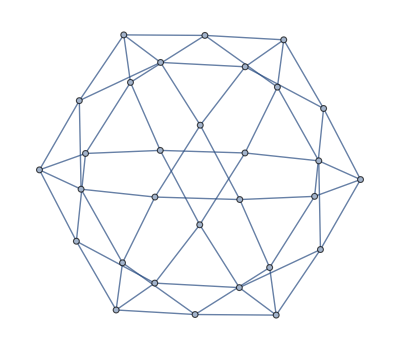

```mathematica
MeshConnectivityGraph[Dodecahedron[],1]
```

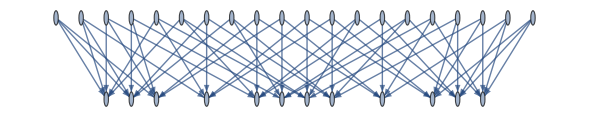

```mathematica
MeshConnectivityGraph[Dodecahedron[],{0,2}]
```

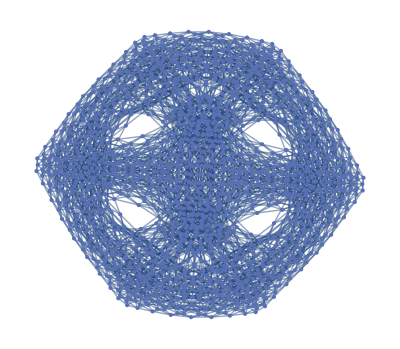
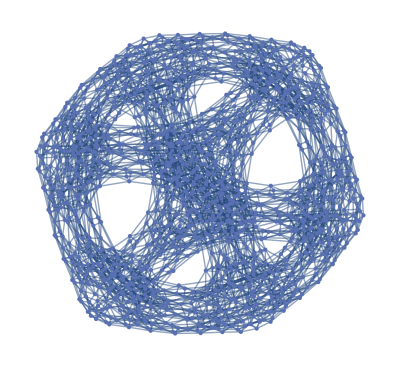
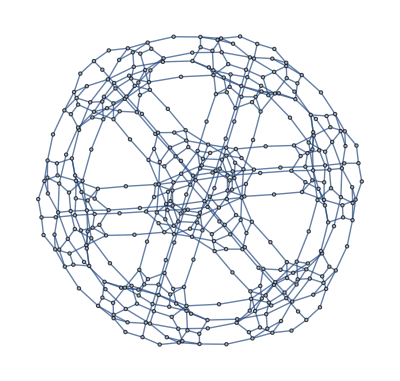
{-Graphics3D-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MeshConnectivityGraph[MengerMesh[2,3],d],{d,0,3}]
```

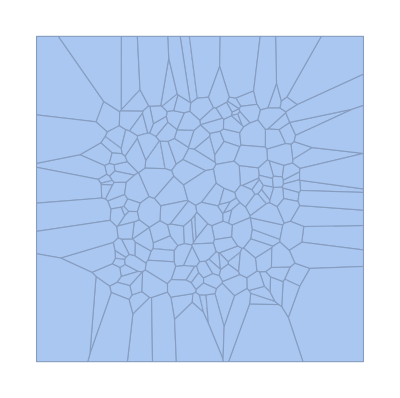

```mathematica
vm=VoronoiMesh[RandomReal[1,{200,2}]]
```

```mathematica
NearestMeshCells[vm,{.5,.5},10]
```

{{2,186},{2,50},{2,194},{2,165},{2,132},{2,63},{2,9},{2,22},{2,48},{2,59}}

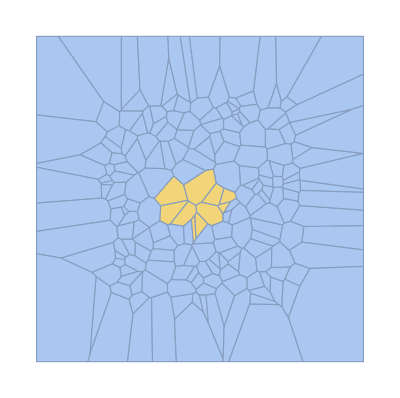

```mathematica
HighlightMesh[vm,%]
```

```mathematica
Dataset[CloudGet["https://wolfr.am/L9o1Pb7V"],MaxItems->{4,3}]
```

```mathematica
Dataset[CloudGet["https://wolfr.am/L9o1Pb7V"],MaxItems->5,HeaderBackground->LightGreen,Background->{{{LightBlue,LightOrange}}},ItemDisplayFunction->{"sex"->(If[#==="female",♀,♂]&)}]
```

```mathematica
TableView[{{5,6},{7,3}}]
```

5673

```mathematica
gpt2=NetModel["GPT-2 Transformer Trained on WebText Data","Task"->"LanguageModeling"]
```

NetChain[<>]

```mathematica
Nest[StringJoin[#,gpt2[#,"RandomSample"]]&,"Stephen Wolfram is",20]
```

Stephen Wolfram is a photojournalist turned blogger and professor at Denver College fossilsologist, curator and kindergartens coordinator

```mathematica
Graph[{Annotation[1->2,EdgeStyle->Red],Annotation[2->1,EdgeStyle->Blue]}]
```

-Graphics-

```mathematica
Graph[{Annotation[x,VertexStyle->Red],Annotation[y,VertexStyle->Blue]},{x->y,y->x,y->y},VertexSize->.2]
```

-Graphics-

```mathematica
AnnotationValue[{%,x},VertexStyle]
```

RGBColor[1, 0, 0]

```mathematica
g=CloudGet["https://wolfr.am/L9rgvixl"];
```

```mathematica
AnnotationValue[{g,x},VertexStyle]=Green
```

RGBColor[0, 1, 0]

```mathematica
g
```

-Graphics-

```mathematica
AnnotationDelete[{g,x},VertexStyle]
```

-Graphics-

```mathematica
Annotate[{CloudGet["https://wolfr.am/L9rpqPJ0"],{3,5}},VertexSize->.3]
```

-Graphics-

```mathematica
Graph[Catenate[Table[Annotation[i->j,EdgeWeight->GCD[i,j]],{i,5},{j,5}]]]
```

-Graphics-

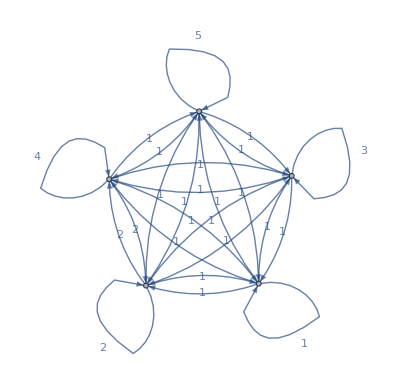

```mathematica
Graph[%,EdgeLabels->"EdgeWeight"]
```

```mathematica
WeightedAdjacencyMatrix[CloudGet["https://wolfr.am/L9rtJdd9"]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 2 | 1
1 | 1 | 3 | 1 | 1
1 | 2 | 1 | 4 | 1
1 | 1 | 1 | 1 | 5)

```mathematica
Graph[{Annotation[x,"age"->10],Annotation[y,"age"->20]},{x->y,y->x,y->y}]
```

-Graphics-

```mathematica
AnnotationValue[{CloudGet["https://wolfr.am/L9rx8Mxe"],x},"age"]
```

10

```mathematica
Options[CloudGet["https://wolfr.am/L9rx8Mxe"],AnnotationRules]
```

{AnnotationRules→{x→{age→10},y→{age→20}}}

```mathematica
TransitiveReductionGraph[CloudGet["https://wolfr.am/L9rBdIZt"]]
```

-Graphics-

```mathematica
Graph[{1->2,1->2}]
```

-Graphics-

```mathematica
EdgeTaggedGraph[{1->2,1->2}->{a,b}]
```

-Graphics-

```mathematica
EdgeList[%]
```

{12a,12b}

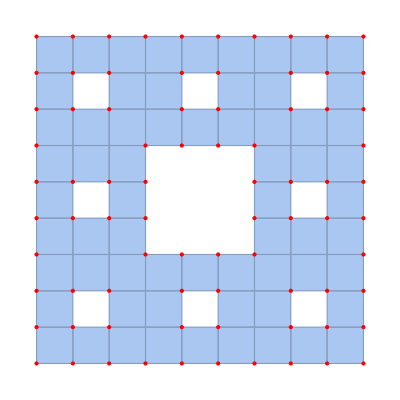

```mathematica
Annotate[{MengerMesh[2],{0,"Boundary"}},MeshCellStyle->Red]
```

```mathematica
AudioAnnotate[ExampleData[{"Audio","MaleVoice"}],"Voiced"]
```

AudioAnnotate::elmntav: "Voiced" is not an available annotation.

AudioAnnotate[,Voiced]

AnnotationValue::pvobj: -- Message text not found -- («1»)

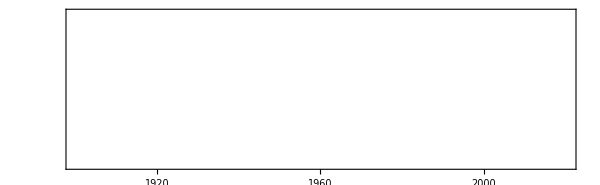

```mathematica
AnnotationValue[%,"Voiced"]//TimelinePlot
```

```mathematica
ImageBoundingBoxes[CloudGet["https://wolfr.am/L9qz1zu4"]]
```

<|elephant→{Rectangle[{433.923,102.865},{553.362,211.964}],Rectangle[{336.372,155.731},{474.614,272.098}],Rectangle[{160.801,107.681},{409.561,262.771}]},zebra→{Rectangle[{35.9317,19.1565},{206.023,159.265}],Rectangle[{3.4649,152.314},{78.4044,211.948}],Rectangle[{133.182,94.3629},{223.032,172.756}]}|>

```mathematica
HighlightImage[CloudGet["https://wolfr.am/L9qz1zu4"],%]
```

-Graphics-

```mathematica
{a,b,Nothing,c,Nothing}
```

{a,b,c}

```mathematica
{a,b,Splice[{x,y,z}],c,d}
```

{a,b,x,y,z,c,d}

```mathematica
Splice[{x,y,z}]
```

Splice[{x,y,z}]

```mathematica
{a,b,x,c,d}/.x->Splice[{p,q,r}]
```

{a,b,p,q,r,c,d}

```mathematica
SubsetCases[{a,b,a,b,a,c},{x_,y_,x_},Overlaps->True]
```

{{a,b,a},{a,b,a},{a,a,a},{a,c,a},{a,b,a},{a,b,a},{a,c,a},{b,a,b},{b,a,b},{b,a,b},{b,c,b},{a,b,a},{a,b,a},{a,c,a}}

```mathematica
Today<InfiniteFuture
```

True

```mathematica
OperatorApplied[f][x][y]
```

f[y,x]

```mathematica
Select[{1,2,3,4},PrimeQ]
```

{2,3}

```mathematica
Select[PrimeQ][{1,2,3,4}]
```

{2,3}

```mathematica
Map[Select[PrimeQ],{{6,7,8},{11,12,13,14}}]
```

{{7},{11,13}}

```mathematica
Select[PrimeQ]
```

Select[PrimeQ]

```mathematica
Map[Select[PrimeQ]][{{6,7,8},{11,12,13,14}}]
```

{{7},{11,13}}

```mathematica
OperatorApplied[f][y]
```

OperatorApplied[f][y]

```mathematica
OperatorApplied[f][y][x]
```

f[x,y]

```mathematica
OperatorApplied[f,4->{3,2,1,4}][x][y][z][u][v]
```

f[z,y,x,u][Video[http://exampledata.wolfram.com/cars.avi,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]http://exampledata.wolfram.com/cars.aviThumbnail1StandardForm]

```mathematica
CurryApplied[f,2][x][y]
```

f[x,y]

```mathematica
CurryApplied[f,2][x][y][z][u][v]
```

f[x,y][z][u][Video[http://exampledata.wolfram.com/cars.avi,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]http://exampledata.wolfram.com/cars.aviThumbnail1StandardForm]

```mathematica
CurryApplied[2][f][x][y][z][u][v]
```

f[x,y][z][u][Video[http://exampledata.wolfram.com/cars.avi,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]http://exampledata.wolfram.com/cars.aviThumbnail1StandardForm]

```mathematica
ReverseApplied[f][x,y,z]
```

f[z,y,x]

```mathematica
Sort[{5,6,1,7,3,7,3},ReverseApplied[NumericalOrder]]
```

{7,7,6,5,3,3,1}

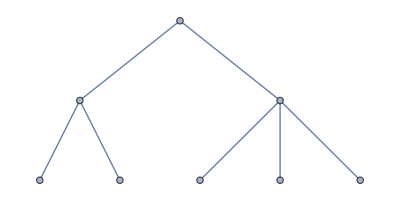

```mathematica
ExpressionGraph[{{a,b},{c,d,e}}]
```

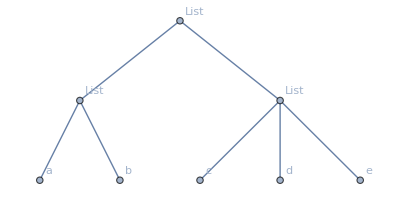

```mathematica
ExpressionGraph[{{a,b},{c,d,e}},VertexLabels->Automatic]
```

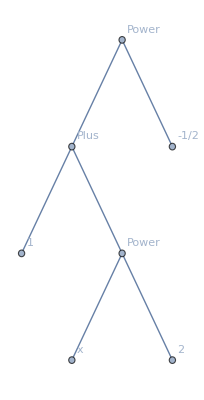

```mathematica
ExpressionGraph[1/(√(1+x^2)),VertexLabels->Automatic]
```

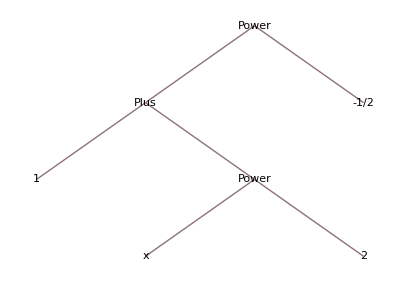

```mathematica
TreeForm@(1/(√(1+x^2)))
```

```mathematica
TimeConstrained[Pause[1];TimeRemaining[],5]
```

3.99859

```mathematica
axioms=AxiomaticTheory[{"GroupAxioms","Multiplication"->p,"Identity"->e}]
```

{∀_{a,b,c}p[a,p[b,c]]==p[p[a,b],c],∀_a p[a,e]==a,∀_a p[a,ā]==e}

```mathematica
FindEquationalProof[p[e,x]==x,axioms]
```

ProofObject[…]

```mathematica
Dataset[%["ProofDataset"],MaxItems->{6,1}]
```

```mathematica
FiniteGroupData["Quaternion","DefiningRelations"]
```

2∘3∘2∘3^(∘-1)==3∘2∘3∘2^(∘-1)==1

```mathematica
AxiomaticTheory[{"GroupAxioms","Quaternion","Multiplication"->p,"Identity"->e}]
```

{∀_{a,b,c}p[a,p[b,c]]==p[p[a,b],c],∀_a p[a,e]==a,∀_a p[a,ā]==e,p[p[f,g],f]==g,p[p[g,f],g]==f}

```mathematica
AxiomaticTheory[{"GroupAxioms","Quaternion",<|"Multiplication"->p,"Inverse"->inv,"Identity"->e,"Generators"->{i,j}|>}]
```

{∀_{a,b,c}p[a,p[b,c]]==p[p[a,b],c],∀_a p[a,e]==a,∀_a p[a,inv[a]]==e,p[p[i,j],i]==j,p[p[j,i],j]==i}

```mathematica
FullForm[%]
```

List[ForAll[List[\[FormalA],\[FormalB],\[FormalC]],Equal[p[\[FormalA],p[\[FormalB],\[FormalC]]],p[p[\[FormalA],\[FormalB]],\[FormalC]]]],ForAll[\[FormalA],Equal[p[\[FormalA],e],\[FormalA]]],ForAll[\[FormalA],Equal[p[\[FormalA],inv[\[FormalA]]],e]],Equal[p[p[i,j],i],j],Equal[p[p[j,i],j],i]]

```mathematica
FindEquationalProof[p[i,p[i,p[i,i]]]==e,%]
```

ProofObject[…]

```mathematica
FindEquationalProof[mortal[socrates],{ForAll[x,Implies[man[x],mortal[x]]],man[socrates]}]
```

ProofObject[…]

```mathematica
FindEquationalProof[Not[Exists[x,And[baby[x],manageCrocodile[x]]]],{ForAll[x,Implies[baby[x],Not[logical[x]]]],ForAll[x,Implies[manageCrocodile[x],Not[despised[x]]]],ForAll[x,Implies[Not[logical[x]],despised[x]]]}]
```

ProofObject[…]

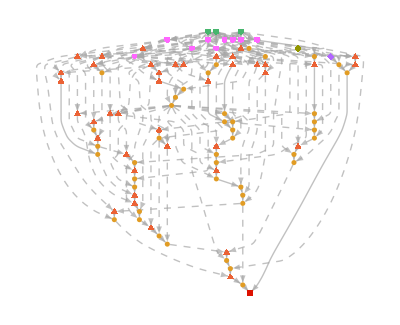

```mathematica
Out[143]["ProofGraph"]
```

```mathematica
Here
```

GeoPosition[{33.9,-118.16}]

```mathematica
GeoIdentify[]
```

{Paramount,United States,California Central District Court,North America,world,America/Los_Angeles,GMT-8,Los Angeles-Long Beach-Santa Ana, CA,California 40th Congressional District,Los Angeles County, California, United States,Paramount Unified School District,California, United States,90723}

```mathematica
RegionCentroid[Polygon[Entity["Country","UnitedStates"]]]
```

GeoPosition[{39.9032,-98.8178,-130877.}]

```mathematica
DiscretizeRegion[Entity["Country","UnitedStates"]["Polygon"]]
```

-Graphics3D-

```mathematica
Area[GeoGridPosition[Entity["Country","Greenland"]["Polygon"],"Mercator"]]
```

2799.88

```mathematica
Area[GeoGridPosition[Entity["Country","Greenland"]["Polygon"],"CylindricalEqualArea"]]
```

169.4

```mathematica
Entity["GoatBreed","OberhasliGoat"]["Image"]
```

-Graphics-

```mathematica
EntityList[EntityClass["GoatBreed","Origin"->Entity["Country","Spain"]]]
```

{Spanish Goat,Verata Goat}

```mathematica
Entity["DogBreed","Chihuahua"]["Image"]
```

-Graphics-

```mathematica
Entity["DogBreed","Chihuahua"]
```

Chihuahua

```mathematica
Entity["DogBreed","Chihuahua"]["Properties"]
```

{AKC recognition year,alternate names,description,entity classes,hair length,female height,female maximum height,female mean height,female minimum height,male height,male maximum height,male mean height,male minimum height,image,life span,litter size,maximum life span,maximum litter size,name,origin,recognized by,shedding,size,temperament,UKC recognition year,female weight,female maximum weight,female mean weight,female minimum weight,male weight,male maximum weight,male mean weight,male minimum weight}

```mathematica
EntityList[EntityClass["GoatBreed","Origin"->Entity["Country","Spain"]]]
```

{Spanish Goat,Verata Goat}

```mathematica
Entity["FoodType","Potato"][EntityProperty["FoodType","ApproximateCookingTimes"]]
```

<|EntityInstance[,1 item]→<|microwave→(5.to7.) min|>,EntityInstance[,1.5 lb]→<|boil→(10.to15.) min,steam→(10.to15.) min,bake→(45.to60.) min,grill→(60.to90.) min,pan fry→(5.to6.) min,roast→(25.to45.) min,deep fry→(5.to8.) min|>,EntityInstance[,2 items]→<|microwave→(10.to12.) min|>,EntityInstance[,4 items]→<|microwave→(10.to12.) min|>,EntityInstance[,1 item]→<|microwave→(1.to2.) min|>,EntityInstance[,2 items]→<|microwave→(2.to3.) min|>,→<|pressure cook→(8.to10.) min|>|>

```mathematica
ExternalIdentifier["ISBN10","1-57955-008-8"]
```

ExternalIdentifier[ISBN10,1-57955-008-8]ISBN-101-57955-008-8urn:ISBN:1-57955-008-8

```mathematica
Entity["FoodType","Potato"][EntityProperty["FoodType","Image"]]
```

-Graphics-

```mathematica
WikidataData[Entity["Person","StephenWolfram::j276d"],"WikidataID"]
```

{ExternalIdentifier[WikidataID,Q310798,<|Label→Stephen Wolfram,Description→British-American computer scientist, mathematician, physicist, writer and businessman|>]WikidataStephen Wolframhttp://www.wikidata.org/entity/Q310798}

```mathematica
InputForm[%]
```

{ExternalIdentifier["WikidataID", "Q310798", 
  <|"Label" -> "Stephen Wolfram", "Description" -> "British-\
American computer scientist, mathematician, physicist, \
writer and businessman"|>]}

```mathematica
WikidataData[Entity["Person","StephenWolfram::j276d"],"Classes"]
```

{ExternalIdentifier[WikidataID,Q5,<|Label→human,Description→common name of Homo sapiens, unique extant species of the genus Homo|>]Wikidatahumanhttp://www.wikidata.org/entity/Q5}

```mathematica
WikidataSearch["hoax"]
```

{ExternalIdentifier[WikidataID,Q190084,<|Label→hoax,Description→deliberately fabricated falsehood made to masquerade as the truth|>]Wikidatahoaxhttp://www.wikidata.org/entity/Q190084,ExternalIdentifier[WikidataID,Q187044,<|Label→canard,Description→false or misleading report or story in printed press|>]Wikidatacanardhttp://www.wikidata.org/entity/Q187044,ExternalIdentifier[WikidataID,Q168821,<|Label→The Hoax,Description→2006 film by Lasse Hallström|>]WikidataThe Hoaxhttp://www.wikidata.org/entity/Q168821,ExternalIdentifier[WikidataID,Q67178312,<|Label→Hoax,Description→episode of S.W.A.T. (S1 E22)|>]WikidataHoaxhttp://www.wikidata.org/entity/Q67178312,ExternalIdentifier[WikidataID,Q28092864,<|Label→Wikimedia hoax,Description→this item is a hoax and can be deleted once the necessary deletions are done in other Wikimedia projects|>]WikidataWikimedia hoaxhttp://www.wikidata.org/entity/Q28092864,ExternalIdentifier[WikidataID,Q1621527,<|Label→Hoax,Description→Wikipedia disambiguation page|>]WikidataHoaxhttp://www.wikidata.org/entity/Q1621527,ExternalIdentifier[WikidataID,Q28196140,<|Label→A Hoax,Description→1936 film by E. W. Emo|>]WikidataA Hoaxhttp://www.wikidata.org/entity/Q28196140,ExternalIdentifier[WikidataID,Q3125142,<|Label→HOAX|>]WikidataHOAXhttp://www.wikidata.org/entity/Q3125142,ExternalIdentifier[WikidataID,Q60750329,<|Label→Hoax,Description→American indie pop band originating in Long Island, New York|>]WikidataHoaxhttp://www.wikidata.org/entity/Q60750329,ExternalIdentifier[WikidataID,Q48673996,<|Label→The Hoax,Description→1972 film directed by Robert Anderson|>]WikidataThe Hoaxhttp://www.wikidata.org/entity/Q48673996}

```mathematica
WikidataData[EntityClass[ExternalIdentifier["WikidataID","Q190084",<|"Label"->"hoax","Description"->"deliberately fabricated falsehood made to masquerade as the truth"|>],All],"WikidataID"]
```

{{ExternalIdentifier[WikidataID,Q185736,<|Label→spaghetti-tree,Description→hoax report broadcast on BBC|>]Wikidataspaghetti-treehttp://www.wikidata.org/entity/Q185736},{ExternalIdentifier[WikidataID,Q212201,<|Label→Priory of Sion,Description→French fraternity|>]WikidataPriory of Sionhttp://www.wikidata.org/entity/Q212201},{ExternalIdentifier[WikidataID,Q219355,<|Label→Roswell UFO incident,Description→Supposed flying saucer crash in the U.S., 1949|>]WikidataRoswell UFO incidenthttp://www.wikidata.org/entity/Q219355},{ExternalIdentifier[WikidataID,Q255935,<|Label→Skvader,Description→fictional animal|>]WikidataSkvaderhttp://www.wikidata.org/entity/Q255935},{ExternalIdentifier[WikidataID,Q275924,<|Label→The Turk,Description→chess automaton hoax|>]WikidataThe Turkhttp://www.wikidata.org/entity/Q275924},{ExternalIdentifier[WikidataID,Q279012,<|Label→Agloe,Description→fictional place in Delaware County, New York|>]WikidataAgloehttp://www.wikidata.org/entity/Q279012},{ExternalIdentifier[WikidataID,Q399369,<|Label→Argleton,Description→phantom settlement that appeared on Google Maps and Google Earth|>]WikidataArgletonhttp://www.wikidata.org/entity/Q399369},{ExternalIdentifier[WikidataID,Q445461,<|Label→Jakob Maria Mierscheid,Description→fictitious politician|>]WikidataJakob Maria Mierscheidhttp://www.wikidata.org/entity/Q445461},{ExternalIdentifier[WikidataID,Q550326,<|Description→Internet hoax|>]WikidataQ550326http://www.wikidata.org/entity/Q550326},{ExternalIdentifier[WikidataID,Q616503,<|Label→Dreadnought hoax,Description→hoax|>]WikidataDreadnought hoaxhttp://www.wikidata.org/entity/Q616503},{ExternalIdentifier[WikidataID,Q717249,<|Label→Tanaka Memorial,Description→alleged Japanese strategic planning document from 1927 in which Prime Minister Baron Tanaka Giichi laid out for Emperor Hirohito a strategy to take over the world|>]WikidataTanaka Memorialhttp://www.wikidata.org/entity/Q717249},{ExternalIdentifier[WikidataID,Q1049105,<|Label→Sokal affair,Description→1996 hoax accepted by an academic journal|>]WikidataSokal affairhttp://www.wikidata.org/entity/Q1049105},{ExternalIdentifier[WikidataID,Q1076259,<|Label→Chopper,Description→hoax ghost in Regensburg, Germany|>]WikidataChopperhttp://www.wikidata.org/entity/Q1076259},{ExternalIdentifier[WikidataID,Q1291575,<|Label→Johann Jakob Feinhals,Description→fictional human|>]WikidataJohann Jakob Feinhalshttp://www.wikidata.org/entity/Q1291575},{ExternalIdentifier[WikidataID,Q2753951,<|Label→Fiji mermaid,Description→fake mummified body of a half-mammal half-fish|>]WikidataFiji mermaidhttp://www.wikidata.org/entity/Q2753951},{ExternalIdentifier[WikidataID,Q2936902,<|Label→Edward Owens hoax,Description→hoaxes|>]WikidataEdward Owens hoaxhttp://www.wikidata.org/entity/Q2936902},{ExternalIdentifier[WikidataID,Q20117,<|Label→dihydrogen monoxide parody,Description→hoax where water is presented by an uncommon name|>]Wikidatadihydrogen monoxide parodyhttp://www.wikidata.org/entity/Q20117},{ExternalIdentifier[WikidataID,Q26193,<|Label→The Protocols of the Elders of Zion,Description→antisemitic hoax-promoting book|>]WikidataThe Protocols of the Elders of Zionhttp://www.wikidata.org/entity/Q26193},{ExternalIdentifier[WikidataID,Q29998065,<|Label→The conceptual penis as a social construct,Description→scientific article (publication date: 19 May 2017)|>]WikidataThe conceptual penis as a social constructhttp://www.wikidata.org/entity/Q29998065},{ExternalIdentifier[WikidataID,Q30001841,<|Label→Transgressing the Boundaries: Towards a Transformative Hermeneutics of Quantum Gravity,Description→academic hoax article that caused the Sokal affair|>]WikidataTransgressing the Boundaries: Towards a Transformative Hermeneutics of Quantum Gravityhttp://www.wikidata.org/entity/Q30001841},{ExternalIdentifier[WikidataID,Q30001874,<|Label→Hermippus redivivus,Description→article by Johann Heinrich Cohausen|>]WikidataHermippus redivivushttp://www.wikidata.org/entity/Q30001874},{ExternalIdentifier[WikidataID,Q39859227,<|Label→Tunnel to the Vatican,Description→conspiracy theory|>]WikidataTunnel to the Vaticanhttp://www.wikidata.org/entity/Q39859227},{ExternalIdentifier[WikidataID,Q48811499,<|Label→2017 Wichita swatting,Description→killing in the United States|>]Wikidata2017 Wichita swattinghttp://www.wikidata.org/entity/Q48811499},{ExternalIdentifier[WikidataID,Q56239871,<|Label→Momo challenge hoax,Description→Internet hoax|>]WikidataMomo challenge hoaxhttp://www.wikidata.org/entity/Q56239871},{ExternalIdentifier[WikidataID,Q56582709,<|Label→Miscegenation,Description→1863 hoax pamphlet|>]WikidataMiscegenationhttp://www.wikidata.org/entity/Q56582709},{ExternalIdentifier[WikidataID,Q57251522,<|Label→"Grievance Studies" affair,Description→2018 group of bogus academic papers|>]Wikidata"Grievance Studies" affairhttp://www.wikidata.org/entity/Q57251522},{ExternalIdentifier[WikidataID,Q63969803,<|Label→FemCon 2015,Description→hoax|>]WikidataFemCon 2015http://www.wikidata.org/entity/Q63969803},{ExternalIdentifier[WikidataID,Q77962285,<|Label→Automobilités postmodernes : quand l’Autolib’ fait sensation à Paris,Description→hoax|>]WikidataAutomobilités postmodernes : quand l’Autolib’ fait sensation à Parishttp://www.wikidata.org/entity/Q77962285},{ExternalIdentifier[WikidataID,Q77963174,<|Label→Ontology, Neutrality and the Strive for (non-)Being-Queer,Description→hoax|>]WikidataOntology, Neutrality and the Strive for (non-)Being-Queerhttp://www.wikidata.org/entity/Q77963174},{ExternalIdentifier[WikidataID,Q81895364,<|Label→#EndFathersDay,Description→hashtag and internet hoax created by the 4chan imageboard /pol/|>]Wikidata#EndFathersDayhttp://www.wikidata.org/entity/Q81895364},{ExternalIdentifier[WikidataID,Q3112607,<|Label→The Balloon-Hoax,Description→newspaper article written by Edgar Allan Poe, first published in 1844, originally presented as a true story, about Monck Mason's trip across the Atlantic Ocean in 3 days in a gas balloon; later revealed as a hoax|>]WikidataThe Balloon-Hoaxhttp://www.wikidata.org/entity/Q3112607},{ExternalIdentifier[WikidataID,Q3133536,<|Label→Well to Hell hoax,Description→urban legend|>]WikidataWell to Hell hoaxhttp://www.wikidata.org/entity/Q3133536},{ExternalIdentifier[WikidataID,Q3502884,<|Label→Beatosu and Goblu,Description→fictional towns|>]WikidataBeatosu and Gobluhttp://www.wikidata.org/entity/Q3502884},{ExternalIdentifier[WikidataID,Q3621611,<|Label→Business Plot,Description→political conspiracy in 1933 in the United States|>]WikidataBusiness Plothttp://www.wikidata.org/entity/Q3621611},{ExternalIdentifier[WikidataID,Q3926183,<|Label→Q33 NY,Description→hoax related to the 9/11 terrorist attacks|>]WikidataQ33 NYhttp://www.wikidata.org/entity/Q3926183},{ExternalIdentifier[WikidataID,Q4614190,<|Label→2009 Latvian meteorite hoax,Description→scientific hoax in Latvia|>]Wikidata2009 Latvian meteorite hoaxhttp://www.wikidata.org/entity/Q4614190},{ExternalIdentifier[WikidataID,Q4659126,<|Label→A Racial Program for the Twentieth Century,Description→antisemitic, anti-Civil Rights Movement, anti-Communist hoax|>]WikidataA Racial Program for the Twentieth Centuryhttp://www.wikidata.org/entity/Q4659126},{ExternalIdentifier[WikidataID,Q4700987,<|Label→Akiko Yamamoto,Description→Female samurai from the early Tokugawa Period|>]WikidataAkiko Yamamotohttp://www.wikidata.org/entity/Q4700987},{ExternalIdentifier[WikidataID,Q4843185,<|Label→Baidu 10 Mythical Creatures,Description→Internet meme in China|>]WikidataBaidu 10 Mythical Creatureshttp://www.wikidata.org/entity/Q4843185},{ExternalIdentifier[WikidataID,Q5287624,<|Label→Document 12-571-3570,Description→fictional NASA document|>]WikidataDocument 12-571-3570http://www.wikidata.org/entity/Q5287624},{ExternalIdentifier[WikidataID,Q5381988,<|Label→Eoörnis pterovelox gobiensis,Description→humorous scientific hoax by Lester W. Sharp|>]WikidataEoörnis pterovelox gobiensishttp://www.wikidata.org/entity/Q5381988},{ExternalIdentifier[WikidataID,Q5583639,<|Label→Goodtimes virus,Description→Internet hoax|>]WikidataGoodtimes virushttp://www.wikidata.org/entity/Q5583639},{ExternalIdentifier[WikidataID,Q5612122,<|Label→Grunge speak,Description→hoax|>]WikidataGrunge speakhttp://www.wikidata.org/entity/Q5612122},{ExternalIdentifier[WikidataID,Q6782491,<|Label→Masal Bugduv,Description→association football player|>]WikidataMasal Bugduvhttp://www.wikidata.org/entity/Q6782491},{ExternalIdentifier[WikidataID,Q6902854,<|Label→Monster of Lake Fagua,Description→fictional lake creature|>]WikidataMonster of Lake Faguahttp://www.wikidata.org/entity/Q6902854},{ExternalIdentifier[WikidataID,Q7494251,<|Label→Sheng Long,Description→fictional character based on a translation error|>]WikidataSheng Longhttp://www.wikidata.org/entity/Q7494251},{ExternalIdentifier[WikidataID,Q12306996,<|Label→Dag Henrik Esrum-Hellerup,Description→fictitious Danish composer|>]WikidataDag Henrik Esrum-Helleruphttp://www.wikidata.org/entity/Q12306996},{ExternalIdentifier[WikidataID,Q16896007,<|Label→Null Island,Description→fictional island at 0°N 0°E|>]WikidataNull Islandhttp://www.wikidata.org/entity/Q16896007},{ExternalIdentifier[WikidataID,Q20191952,<|Label→Jar'Edo Wens hoax,Description→hoax|>]WikidataJar'Edo Wens hoaxhttp://www.wikidata.org/entity/Q20191952},{ExternalIdentifier[WikidataID,Q21510193,<|Label→Bicholim conflict,Description→Wikipedia hoax that received the "Good Article" status before it was deleted|>]WikidataBicholim conflicthttp://www.wikidata.org/entity/Q21510193},{ExternalIdentifier[WikidataID,Q24256259,<|Label→Enigmarelle,Description→fake automaton around 1905|>]WikidataEnigmarellehttp://www.wikidata.org/entity/Q24256259},{ExternalIdentifier[WikidataID,Q28652506,<|Label→Bowling Green massacre,Description→a fictitious incident of terrorism mentioned by U.S. Counselor to the President Kellyanne Conway in interviews with Cosmopolitan and TMZ on January 29, 2017|>]WikidataBowling Green massacrehttp://www.wikidata.org/entity/Q28652506},{ExternalIdentifier[WikidataID,Q300495,<|Label→Bathtub hoax|>]WikidataBathtub hoaxhttp://www.wikidata.org/entity/Q300495},{ExternalIdentifier[WikidataID,Q1574780,<|Label→Good Wife's Guide|>]WikidataGood Wife's Guidehttp://www.wikidata.org/entity/Q1574780},{ExternalIdentifier[WikidataID,Q1977671,<|Label→humanitarian bombing|>]Wikidatahumanitarian bombinghttp://www.wikidata.org/entity/Q1977671},{ExternalIdentifier[WikidataID,Q2727395]WikidataQ2727395http://www.wikidata.org/entity/Q2727395},{ExternalIdentifier[WikidataID,Q3576433,<|Label→Zzxjoanw|>]WikidataZzxjoanwhttp://www.wikidata.org/entity/Q3576433},{ExternalIdentifier[WikidataID,Q3903568,<|Label→AVM Runestone|>]WikidataAVM Runestonehttp://www.wikidata.org/entity/Q3903568},{ExternalIdentifier[WikidataID,Q4425652,<|Label→Great Wall of China hoax|>]WikidataGreat Wall of China hoaxhttp://www.wikidata.org/entity/Q4425652},{ExternalIdentifier[WikidataID,Q4698578,<|Label→Aircruise|>]WikidataAircruisehttp://www.wikidata.org/entity/Q4698578},{ExternalIdentifier[WikidataID,Q4805611,<|Label→Ashley Todd mugging hoax|>]WikidataAshley Todd mugging hoaxhttp://www.wikidata.org/entity/Q4805611},{ExternalIdentifier[WikidataID,Q4987248,<|Label→Bulb to light all Ramat Gan|>]WikidataBulb to light all Ramat Ganhttp://www.wikidata.org/entity/Q4987248},{ExternalIdentifier[WikidataID,Q5600039,<|Label→Great Stock Exchange Fraud of 1814|>]WikidataGreat Stock Exchange Fraud of 1814http://www.wikidata.org/entity/Q5600039},{ExternalIdentifier[WikidataID,Q5970122,<|Label→ID Sniper rifle|>]WikidataID Sniper riflehttp://www.wikidata.org/entity/Q5970122},{ExternalIdentifier[WikidataID,Q6475961,<|Label→Lake George Monster|>]WikidataLake George Monsterhttp://www.wikidata.org/entity/Q6475961},{ExternalIdentifier[WikidataID,Q6749224,<|Label→Manhattan Airport Foundation|>]WikidataManhattan Airport Foundationhttp://www.wikidata.org/entity/Q6749224},{ExternalIdentifier[WikidataID,Q6775381,<|Label→Martin Eisenstadt|>]WikidataMartin Eisenstadthttp://www.wikidata.org/entity/Q6775381},{ExternalIdentifier[WikidataID,Q7358108,<|Label→Roger Dodsworth|>]WikidataRoger Dodsworthhttp://www.wikidata.org/entity/Q7358108},{ExternalIdentifier[WikidataID,Q7415312,<|Label→San Serriffe|>]WikidataSan Serriffehttp://www.wikidata.org/entity/Q7415312},{ExternalIdentifier[WikidataID,Q7857205,<|Label→Tuxissa|>]WikidataTuxissahttp://www.wikidata.org/entity/Q7857205},{ExternalIdentifier[WikidataID,Q9397878]WikidataQ9397878http://www.wikidata.org/entity/Q9397878},{ExternalIdentifier[WikidataID,Q12341894,<|Label→Æblerød|>]WikidataÆblerødhttp://www.wikidata.org/entity/Q12341894},{ExternalIdentifier[WikidataID,Q15918255]WikidataQ15918255http://www.wikidata.org/entity/Q15918255},{ExternalIdentifier[WikidataID,Q19025254,<|Label→Passengers Safely Moved and Steamer Titanic Taken in Tow|>]WikidataPassengers Safely Moved and Steamer Titanic Taken in Towhttp://www.wikidata.org/entity/Q19025254},{ExternalIdentifier[WikidataID,Q19852065,<|Label→Tainan fake panda incident|>]WikidataTainan fake panda incidenthttp://www.wikidata.org/entity/Q19852065},{ExternalIdentifier[WikidataID,Q19892098,<|Label→Borghild Project|>]WikidataBorghild Projecthttp://www.wikidata.org/entity/Q19892098},{ExternalIdentifier[WikidataID,Q22906035,<|Label→2015 Voluntary non-work day|>]Wikidata2015 Voluntary non-work dayhttp://www.wikidata.org/entity/Q22906035},{ExternalIdentifier[WikidataID,Q39091225,<|Label→1967 British flying saucer hoax|>]Wikidata1967 British flying saucer hoaxhttp://www.wikidata.org/entity/Q39091225},{ExternalIdentifier[WikidataID,Q54439213,<|Label→staged murder of Arkadiy Babchenko|>]Wikidatastaged murder of Arkadiy Babchenkohttp://www.wikidata.org/entity/Q54439213},{ExternalIdentifier[WikidataID,Q55641486,<|Label→Pot brownies food stamps hoax|>]WikidataPot brownies food stamps hoaxhttp://www.wikidata.org/entity/Q55641486}}

```mathematica
WikidataData[EntityClass[ExternalIdentifier["WikidataID","Q190084",<|"Label"->"hoax","Description"->"deliberately fabricated falsehood made to masquerade as the truth"|>],All],"WikidataID"]
```

{{ExternalIdentifier[WikidataID,Q185736,<|Label→spaghetti-tree,Description→hoax report broadcast on BBC|>]Wikidataspaghetti-treehttp://www.wikidata.org/entity/Q185736},{ExternalIdentifier[WikidataID,Q212201,<|Label→Priory of Sion,Description→French fraternity|>]WikidataPriory of Sionhttp://www.wikidata.org/entity/Q212201},{ExternalIdentifier[WikidataID,Q219355,<|Label→Roswell UFO incident,Description→Supposed flying saucer crash in the U.S., 1949|>]WikidataRoswell UFO incidenthttp://www.wikidata.org/entity/Q219355},{ExternalIdentifier[WikidataID,Q255935,<|Label→Skvader,Description→fictional animal|>]WikidataSkvaderhttp://www.wikidata.org/entity/Q255935},{ExternalIdentifier[WikidataID,Q275924,<|Label→The Turk,Description→chess automaton hoax|>]WikidataThe Turkhttp://www.wikidata.org/entity/Q275924},{ExternalIdentifier[WikidataID,Q279012,<|Label→Agloe,Description→fictional place in Delaware County, New York|>]WikidataAgloehttp://www.wikidata.org/entity/Q279012},{ExternalIdentifier[WikidataID,Q399369,<|Label→Argleton,Description→phantom settlement that appeared on Google Maps and Google Earth|>]WikidataArgletonhttp://www.wikidata.org/entity/Q399369},{ExternalIdentifier[WikidataID,Q445461,<|Label→Jakob Maria Mierscheid,Description→fictitious politician|>]WikidataJakob Maria Mierscheidhttp://www.wikidata.org/entity/Q445461},{ExternalIdentifier[WikidataID,Q550326,<|Description→Internet hoax|>]WikidataQ550326http://www.wikidata.org/entity/Q550326},{ExternalIdentifier[WikidataID,Q616503,<|Label→Dreadnought hoax,Description→hoax|>]WikidataDreadnought hoaxhttp://www.wikidata.org/entity/Q616503},{ExternalIdentifier[WikidataID,Q717249,<|Label→Tanaka Memorial,Description→alleged Japanese strategic planning document from 1927 in which Prime Minister Baron Tanaka Giichi laid out for Emperor Hirohito a strategy to take over the world|>]WikidataTanaka Memorialhttp://www.wikidata.org/entity/Q717249},{ExternalIdentifier[WikidataID,Q1049105,<|Label→Sokal affair,Description→1996 hoax accepted by an academic journal|>]WikidataSokal affairhttp://www.wikidata.org/entity/Q1049105},{ExternalIdentifier[WikidataID,Q1076259,<|Label→Chopper,Description→hoax ghost in Regensburg, Germany|>]WikidataChopperhttp://www.wikidata.org/entity/Q1076259},{ExternalIdentifier[WikidataID,Q1291575,<|Label→Johann Jakob Feinhals,Description→fictional human|>]WikidataJohann Jakob Feinhalshttp://www.wikidata.org/entity/Q1291575},{ExternalIdentifier[WikidataID,Q2753951,<|Label→Fiji mermaid,Description→fake mummified body of a half-mammal half-fish|>]WikidataFiji mermaidhttp://www.wikidata.org/entity/Q2753951},{ExternalIdentifier[WikidataID,Q2936902,<|Label→Edward Owens hoax,Description→hoaxes|>]WikidataEdward Owens hoaxhttp://www.wikidata.org/entity/Q2936902},{ExternalIdentifier[WikidataID,Q20117,<|Label→dihydrogen monoxide parody,Description→hoax where water is presented by an uncommon name|>]Wikidatadihydrogen monoxide parodyhttp://www.wikidata.org/entity/Q20117},{ExternalIdentifier[WikidataID,Q26193,<|Label→The Protocols of the Elders of Zion,Description→antisemitic hoax-promoting book|>]WikidataThe Protocols of the Elders of Zionhttp://www.wikidata.org/entity/Q26193},{ExternalIdentifier[WikidataID,Q29998065,<|Label→The conceptual penis as a social construct,Description→scientific article (publication date: 19 May 2017)|>]WikidataThe conceptual penis as a social constructhttp://www.wikidata.org/entity/Q29998065},{ExternalIdentifier[WikidataID,Q30001841,<|Label→Transgressing the Boundaries: Towards a Transformative Hermeneutics of Quantum Gravity,Description→academic hoax article that caused the Sokal affair|>]WikidataTransgressing the Boundaries: Towards a Transformative Hermeneutics of Quantum Gravityhttp://www.wikidata.org/entity/Q30001841},{ExternalIdentifier[WikidataID,Q30001874,<|Label→Hermippus redivivus,Description→article by Johann Heinrich Cohausen|>]WikidataHermippus redivivushttp://www.wikidata.org/entity/Q30001874},{ExternalIdentifier[WikidataID,Q39859227,<|Label→Tunnel to the Vatican,Description→conspiracy theory|>]WikidataTunnel to the Vaticanhttp://www.wikidata.org/entity/Q39859227},{ExternalIdentifier[WikidataID,Q48811499,<|Label→2017 Wichita swatting,Description→killing in the United States|>]Wikidata2017 Wichita swattinghttp://www.wikidata.org/entity/Q48811499},{ExternalIdentifier[WikidataID,Q56239871,<|Label→Momo challenge hoax,Description→Internet hoax|>]WikidataMomo challenge hoaxhttp://www.wikidata.org/entity/Q56239871},{ExternalIdentifier[WikidataID,Q56582709,<|Label→Miscegenation,Description→1863 hoax pamphlet|>]WikidataMiscegenationhttp://www.wikidata.org/entity/Q56582709},{ExternalIdentifier[WikidataID,Q57251522,<|Label→"Grievance Studies" affair,Description→2018 group of bogus academic papers|>]Wikidata"Grievance Studies" affairhttp://www.wikidata.org/entity/Q57251522},{ExternalIdentifier[WikidataID,Q63969803,<|Label→FemCon 2015,Description→hoax|>]WikidataFemCon 2015http://www.wikidata.org/entity/Q63969803},{ExternalIdentifier[WikidataID,Q77962285,<|Label→Automobilités postmodernes : quand l’Autolib’ fait sensation à Paris,Description→hoax|>]WikidataAutomobilités postmodernes : quand l’Autolib’ fait sensation à Parishttp://www.wikidata.org/entity/Q77962285},{ExternalIdentifier[WikidataID,Q77963174,<|Label→Ontology, Neutrality and the Strive for (non-)Being-Queer,Description→hoax|>]WikidataOntology, Neutrality and the Strive for (non-)Being-Queerhttp://www.wikidata.org/entity/Q77963174},{ExternalIdentifier[WikidataID,Q81895364,<|Label→#EndFathersDay,Description→hashtag and internet hoax created by the 4chan imageboard /pol/|>]Wikidata#EndFathersDayhttp://www.wikidata.org/entity/Q81895364},{ExternalIdentifier[WikidataID,Q3112607,<|Label→The Balloon-Hoax,Description→newspaper article written by Edgar Allan Poe, first published in 1844, originally presented as a true story, about Monck Mason's trip across the Atlantic Ocean in 3 days in a gas balloon; later revealed as a hoax|>]WikidataThe Balloon-Hoaxhttp://www.wikidata.org/entity/Q3112607},{ExternalIdentifier[WikidataID,Q3133536,<|Label→Well to Hell hoax,Description→urban legend|>]WikidataWell to Hell hoaxhttp://www.wikidata.org/entity/Q3133536},{ExternalIdentifier[WikidataID,Q3502884,<|Label→Beatosu and Goblu,Description→fictional towns|>]WikidataBeatosu and Gobluhttp://www.wikidata.org/entity/Q3502884},{ExternalIdentifier[WikidataID,Q3621611,<|Label→Business Plot,Description→political conspiracy in 1933 in the United States|>]WikidataBusiness Plothttp://www.wikidata.org/entity/Q3621611},{ExternalIdentifier[WikidataID,Q3926183,<|Label→Q33 NY,Description→hoax related to the 9/11 terrorist attacks|>]WikidataQ33 NYhttp://www.wikidata.org/entity/Q3926183},{ExternalIdentifier[WikidataID,Q4614190,<|Label→2009 Latvian meteorite hoax,Description→scientific hoax in Latvia|>]Wikidata2009 Latvian meteorite hoaxhttp://www.wikidata.org/entity/Q4614190},{ExternalIdentifier[WikidataID,Q4659126,<|Label→A Racial Program for the Twentieth Century,Description→antisemitic, anti-Civil Rights Movement, anti-Communist hoax|>]WikidataA Racial Program for the Twentieth Centuryhttp://www.wikidata.org/entity/Q4659126},{ExternalIdentifier[WikidataID,Q4700987,<|Label→Akiko Yamamoto,Description→Female samurai from the early Tokugawa Period|>]WikidataAkiko Yamamotohttp://www.wikidata.org/entity/Q4700987},{ExternalIdentifier[WikidataID,Q4843185,<|Label→Baidu 10 Mythical Creatures,Description→Internet meme in China|>]WikidataBaidu 10 Mythical Creatureshttp://www.wikidata.org/entity/Q4843185},{ExternalIdentifier[WikidataID,Q5287624,<|Label→Document 12-571-3570,Description→fictional NASA document|>]WikidataDocument 12-571-3570http://www.wikidata.org/entity/Q5287624},{ExternalIdentifier[WikidataID,Q5381988,<|Label→Eoörnis pterovelox gobiensis,Description→humorous scientific hoax by Lester W. Sharp|>]WikidataEoörnis pterovelox gobiensishttp://www.wikidata.org/entity/Q5381988},{ExternalIdentifier[WikidataID,Q5583639,<|Label→Goodtimes virus,Description→Internet hoax|>]WikidataGoodtimes virushttp://www.wikidata.org/entity/Q5583639},{ExternalIdentifier[WikidataID,Q5612122,<|Label→Grunge speak,Description→hoax|>]WikidataGrunge speakhttp://www.wikidata.org/entity/Q5612122},{ExternalIdentifier[WikidataID,Q6782491,<|Label→Masal Bugduv,Description→association football player|>]WikidataMasal Bugduvhttp://www.wikidata.org/entity/Q6782491},{ExternalIdentifier[WikidataID,Q6902854,<|Label→Monster of Lake Fagua,Description→fictional lake creature|>]WikidataMonster of Lake Faguahttp://www.wikidata.org/entity/Q6902854},{ExternalIdentifier[WikidataID,Q7494251,<|Label→Sheng Long,Description→fictional character based on a translation error|>]WikidataSheng Longhttp://www.wikidata.org/entity/Q7494251},{ExternalIdentifier[WikidataID,Q12306996,<|Label→Dag Henrik Esrum-Hellerup,Description→fictitious Danish composer|>]WikidataDag Henrik Esrum-Helleruphttp://www.wikidata.org/entity/Q12306996},{ExternalIdentifier[WikidataID,Q16896007,<|Label→Null Island,Description→fictional island at 0°N 0°E|>]WikidataNull Islandhttp://www.wikidata.org/entity/Q16896007},{ExternalIdentifier[WikidataID,Q20191952,<|Label→Jar'Edo Wens hoax,Description→hoax|>]WikidataJar'Edo Wens hoaxhttp://www.wikidata.org/entity/Q20191952},{ExternalIdentifier[WikidataID,Q21510193,<|Label→Bicholim conflict,Description→Wikipedia hoax that received the "Good Article" status before it was deleted|>]WikidataBicholim conflicthttp://www.wikidata.org/entity/Q21510193},{ExternalIdentifier[WikidataID,Q24256259,<|Label→Enigmarelle,Description→fake automaton around 1905|>]WikidataEnigmarellehttp://www.wikidata.org/entity/Q24256259},{ExternalIdentifier[WikidataID,Q28652506,<|Label→Bowling Green massacre,Description→a fictitious incident of terrorism mentioned by U.S. Counselor to the President Kellyanne Conway in interviews with Cosmopolitan and TMZ on January 29, 2017|>]WikidataBowling Green massacrehttp://www.wikidata.org/entity/Q28652506},{ExternalIdentifier[WikidataID,Q300495,<|Label→Bathtub hoax|>]WikidataBathtub hoaxhttp://www.wikidata.org/entity/Q300495},{ExternalIdentifier[WikidataID,Q1574780,<|Label→Good Wife's Guide|>]WikidataGood Wife's Guidehttp://www.wikidata.org/entity/Q1574780},{ExternalIdentifier[WikidataID,Q1977671,<|Label→humanitarian bombing|>]Wikidatahumanitarian bombinghttp://www.wikidata.org/entity/Q1977671},{ExternalIdentifier[WikidataID,Q2727395]WikidataQ2727395http://www.wikidata.org/entity/Q2727395},{ExternalIdentifier[WikidataID,Q3576433,<|Label→Zzxjoanw|>]WikidataZzxjoanwhttp://www.wikidata.org/entity/Q3576433},{ExternalIdentifier[WikidataID,Q3903568,<|Label→AVM Runestone|>]WikidataAVM Runestonehttp://www.wikidata.org/entity/Q3903568},{ExternalIdentifier[WikidataID,Q4425652,<|Label→Great Wall of China hoax|>]WikidataGreat Wall of China hoaxhttp://www.wikidata.org/entity/Q4425652},{ExternalIdentifier[WikidataID,Q4698578,<|Label→Aircruise|>]WikidataAircruisehttp://www.wikidata.org/entity/Q4698578},{ExternalIdentifier[WikidataID,Q4805611,<|Label→Ashley Todd mugging hoax|>]WikidataAshley Todd mugging hoaxhttp://www.wikidata.org/entity/Q4805611},{ExternalIdentifier[WikidataID,Q4987248,<|Label→Bulb to light all Ramat Gan|>]WikidataBulb to light all Ramat Ganhttp://www.wikidata.org/entity/Q4987248},{ExternalIdentifier[WikidataID,Q5600039,<|Label→Great Stock Exchange Fraud of 1814|>]WikidataGreat Stock Exchange Fraud of 1814http://www.wikidata.org/entity/Q5600039},{ExternalIdentifier[WikidataID,Q5970122,<|Label→ID Sniper rifle|>]WikidataID Sniper riflehttp://www.wikidata.org/entity/Q5970122},{ExternalIdentifier[WikidataID,Q6475961,<|Label→Lake George Monster|>]WikidataLake George Monsterhttp://www.wikidata.org/entity/Q6475961},{ExternalIdentifier[WikidataID,Q6749224,<|Label→Manhattan Airport Foundation|>]WikidataManhattan Airport Foundationhttp://www.wikidata.org/entity/Q6749224},{ExternalIdentifier[WikidataID,Q6775381,<|Label→Martin Eisenstadt|>]WikidataMartin Eisenstadthttp://www.wikidata.org/entity/Q6775381},{ExternalIdentifier[WikidataID,Q7358108,<|Label→Roger Dodsworth|>]WikidataRoger Dodsworthhttp://www.wikidata.org/entity/Q7358108},{ExternalIdentifier[WikidataID,Q7415312,<|Label→San Serriffe|>]WikidataSan Serriffehttp://www.wikidata.org/entity/Q7415312},{ExternalIdentifier[WikidataID,Q7857205,<|Label→Tuxissa|>]WikidataTuxissahttp://www.wikidata.org/entity/Q7857205},{ExternalIdentifier[WikidataID,Q9397878]WikidataQ9397878http://www.wikidata.org/entity/Q9397878},{ExternalIdentifier[WikidataID,Q12341894,<|Label→Æblerød|>]WikidataÆblerødhttp://www.wikidata.org/entity/Q12341894},{ExternalIdentifier[WikidataID,Q15918255]WikidataQ15918255http://www.wikidata.org/entity/Q15918255},{ExternalIdentifier[WikidataID,Q19025254,<|Label→Passengers Safely Moved and Steamer Titanic Taken in Tow|>]WikidataPassengers Safely Moved and Steamer Titanic Taken in Towhttp://www.wikidata.org/entity/Q19025254},{ExternalIdentifier[WikidataID,Q19852065,<|Label→Tainan fake panda incident|>]WikidataTainan fake panda incidenthttp://www.wikidata.org/entity/Q19852065},{ExternalIdentifier[WikidataID,Q19892098,<|Label→Borghild Project|>]WikidataBorghild Projecthttp://www.wikidata.org/entity/Q19892098},{ExternalIdentifier[WikidataID,Q22906035,<|Label→2015 Voluntary non-work day|>]Wikidata2015 Voluntary non-work dayhttp://www.wikidata.org/entity/Q22906035},{ExternalIdentifier[WikidataID,Q39091225,<|Label→1967 British flying saucer hoax|>]Wikidata1967 British flying saucer hoaxhttp://www.wikidata.org/entity/Q39091225},{ExternalIdentifier[WikidataID,Q54439213,<|Label→staged murder of Arkadiy Babchenko|>]Wikidatastaged murder of Arkadiy Babchenkohttp://www.wikidata.org/entity/Q54439213},{ExternalIdentifier[WikidataID,Q55641486,<|Label→Pot brownies food stamps hoax|>]WikidataPot brownies food stamps hoaxhttp://www.wikidata.org/entity/Q55641486}}

```mathematica
WikidataData[EntityClass[ExternalIdentifier["WikidataID","Q190084",<|"Label"->"hoax","Description"->"deliberately fabricated falsehood made to masquerade as the truth"|>],All],"WikidataID"]
```

{{ExternalIdentifier[WikidataID,Q185736,<|Label→spaghetti-tree,Description→hoax report broadcast on BBC|>]Wikidataspaghetti-treehttp://www.wikidata.org/entity/Q185736},{ExternalIdentifier[WikidataID,Q212201,<|Label→Priory of Sion,Description→French fraternity|>]WikidataPriory of Sionhttp://www.wikidata.org/entity/Q212201},{ExternalIdentifier[WikidataID,Q219355,<|Label→Roswell UFO incident,Description→Supposed flying saucer crash in the U.S., 1949|>]WikidataRoswell UFO incidenthttp://www.wikidata.org/entity/Q219355},{ExternalIdentifier[WikidataID,Q255935,<|Label→Skvader,Description→fictional animal|>]WikidataSkvaderhttp://www.wikidata.org/entity/Q255935},{ExternalIdentifier[WikidataID,Q275924,<|Label→The Turk,Description→chess automaton hoax|>]WikidataThe Turkhttp://www.wikidata.org/entity/Q275924},{ExternalIdentifier[WikidataID,Q279012,<|Label→Agloe,Description→fictional place in Delaware County, New York|>]WikidataAgloehttp://www.wikidata.org/entity/Q279012},{ExternalIdentifier[WikidataID,Q399369,<|Label→Argleton,Description→phantom settlement that appeared on Google Maps and Google Earth|>]WikidataArgletonhttp://www.wikidata.org/entity/Q399369},{ExternalIdentifier[WikidataID,Q445461,<|Label→Jakob Maria Mierscheid,Description→fictitious politician|>]WikidataJakob Maria Mierscheidhttp://www.wikidata.org/entity/Q445461},{ExternalIdentifier[WikidataID,Q550326,<|Description→Internet hoax|>]WikidataQ550326http://www.wikidata.org/entity/Q550326},{ExternalIdentifier[WikidataID,Q616503,<|Label→Dreadnought hoax,Description→hoax|>]WikidataDreadnought hoaxhttp://www.wikidata.org/entity/Q616503},{ExternalIdentifier[WikidataID,Q717249,<|Label→Tanaka Memorial,Description→alleged Japanese strategic planning document from 1927 in which Prime Minister Baron Tanaka Giichi laid out for Emperor Hirohito a strategy to take over the world|>]WikidataTanaka Memorialhttp://www.wikidata.org/entity/Q717249},{ExternalIdentifier[WikidataID,Q1049105,<|Label→Sokal affair,Description→1996 hoax accepted by an academic journal|>]WikidataSokal affairhttp://www.wikidata.org/entity/Q1049105},{ExternalIdentifier[WikidataID,Q1076259,<|Label→Chopper,Description→hoax ghost in Regensburg, Germany|>]WikidataChopperhttp://www.wikidata.org/entity/Q1076259},{ExternalIdentifier[WikidataID,Q1291575,<|Label→Johann Jakob Feinhals,Description→fictional human|>]WikidataJohann Jakob Feinhalshttp://www.wikidata.org/entity/Q1291575},{ExternalIdentifier[WikidataID,Q2753951,<|Label→Fiji mermaid,Description→fake mummified body of a half-mammal half-fish|>]WikidataFiji mermaidhttp://www.wikidata.org/entity/Q2753951},{ExternalIdentifier[WikidataID,Q2936902,<|Label→Edward Owens hoax,Description→hoaxes|>]WikidataEdward Owens hoaxhttp://www.wikidata.org/entity/Q2936902},{ExternalIdentifier[WikidataID,Q20117,<|Label→dihydrogen monoxide parody,Description→hoax where water is presented by an uncommon name|>]Wikidatadihydrogen monoxide parodyhttp://www.wikidata.org/entity/Q20117},{ExternalIdentifier[WikidataID,Q26193,<|Label→The Protocols of the Elders of Zion,Description→antisemitic hoax-promoting book|>]WikidataThe Protocols of the Elders of Zionhttp://www.wikidata.org/entity/Q26193},{ExternalIdentifier[WikidataID,Q29998065,<|Label→The conceptual penis as a social construct,Description→scientific article (publication date: 19 May 2017)|>]WikidataThe conceptual penis as a social constructhttp://www.wikidata.org/entity/Q29998065},{ExternalIdentifier[WikidataID,Q30001841,<|Label→Transgressing the Boundaries: Towards a Transformative Hermeneutics of Quantum Gravity,Description→academic hoax article that caused the Sokal affair|>]WikidataTransgressing the Boundaries: Towards a Transformative Hermeneutics of Quantum Gravityhttp://www.wikidata.org/entity/Q30001841},{ExternalIdentifier[WikidataID,Q30001874,<|Label→Hermippus redivivus,Description→article by Johann Heinrich Cohausen|>]WikidataHermippus redivivushttp://www.wikidata.org/entity/Q30001874},{ExternalIdentifier[WikidataID,Q39859227,<|Label→Tunnel to the Vatican,Description→conspiracy theory|>]WikidataTunnel to the Vaticanhttp://www.wikidata.org/entity/Q39859227},{ExternalIdentifier[WikidataID,Q48811499,<|Label→2017 Wichita swatting,Description→killing in the United States|>]Wikidata2017 Wichita swattinghttp://www.wikidata.org/entity/Q48811499},{ExternalIdentifier[WikidataID,Q56239871,<|Label→Momo challenge hoax,Description→Internet hoax|>]WikidataMomo challenge hoaxhttp://www.wikidata.org/entity/Q56239871},{ExternalIdentifier[WikidataID,Q56582709,<|Label→Miscegenation,Description→1863 hoax pamphlet|>]WikidataMiscegenationhttp://www.wikidata.org/entity/Q56582709},{ExternalIdentifier[WikidataID,Q57251522,<|Label→"Grievance Studies" affair,Description→2018 group of bogus academic papers|>]Wikidata"Grievance Studies" affairhttp://www.wikidata.org/entity/Q57251522},{ExternalIdentifier[WikidataID,Q63969803,<|Label→FemCon 2015,Description→hoax|>]WikidataFemCon 2015http://www.wikidata.org/entity/Q63969803},{ExternalIdentifier[WikidataID,Q77962285,<|Label→Automobilités postmodernes : quand l’Autolib’ fait sensation à Paris,Description→hoax|>]WikidataAutomobilités postmodernes : quand l’Autolib’ fait sensation à Parishttp://www.wikidata.org/entity/Q77962285},{ExternalIdentifier[WikidataID,Q77963174,<|Label→Ontology, Neutrality and the Strive for (non-)Being-Queer,Description→hoax|>]WikidataOntology, Neutrality and the Strive for (non-)Being-Queerhttp://www.wikidata.org/entity/Q77963174},{ExternalIdentifier[WikidataID,Q81895364,<|Label→#EndFathersDay,Description→hashtag and internet hoax created by the 4chan imageboard /pol/|>]Wikidata#EndFathersDayhttp://www.wikidata.org/entity/Q81895364},{ExternalIdentifier[WikidataID,Q3112607,<|Label→The Balloon-Hoax,Description→newspaper article written by Edgar Allan Poe, first published in 1844, originally presented as a true story, about Monck Mason's trip across the Atlantic Ocean in 3 days in a gas balloon; later revealed as a hoax|>]WikidataThe Balloon-Hoaxhttp://www.wikidata.org/entity/Q3112607},{ExternalIdentifier[WikidataID,Q3133536,<|Label→Well to Hell hoax,Description→urban legend|>]WikidataWell to Hell hoaxhttp://www.wikidata.org/entity/Q3133536},{ExternalIdentifier[WikidataID,Q3502884,<|Label→Beatosu and Goblu,Description→fictional towns|>]WikidataBeatosu and Gobluhttp://www.wikidata.org/entity/Q3502884},{ExternalIdentifier[WikidataID,Q3621611,<|Label→Business Plot,Description→political conspiracy in 1933 in the United States|>]WikidataBusiness Plothttp://www.wikidata.org/entity/Q3621611},{ExternalIdentifier[WikidataID,Q3926183,<|Label→Q33 NY,Description→hoax related to the 9/11 terrorist attacks|>]WikidataQ33 NYhttp://www.wikidata.org/entity/Q3926183},{ExternalIdentifier[WikidataID,Q4614190,<|Label→2009 Latvian meteorite hoax,Description→scientific hoax in Latvia|>]Wikidata2009 Latvian meteorite hoaxhttp://www.wikidata.org/entity/Q4614190},{ExternalIdentifier[WikidataID,Q4659126,<|Label→A Racial Program for the Twentieth Century,Description→antisemitic, anti-Civil Rights Movement, anti-Communist hoax|>]WikidataA Racial Program for the Twentieth Centuryhttp://www.wikidata.org/entity/Q4659126},{ExternalIdentifier[WikidataID,Q4700987,<|Label→Akiko Yamamoto,Description→Female samurai from the early Tokugawa Period|>]WikidataAkiko Yamamotohttp://www.wikidata.org/entity/Q4700987},{ExternalIdentifier[WikidataID,Q4843185,<|Label→Baidu 10 Mythical Creatures,Description→Internet meme in China|>]WikidataBaidu 10 Mythical Creatureshttp://www.wikidata.org/entity/Q4843185},{ExternalIdentifier[WikidataID,Q5287624,<|Label→Document 12-571-3570,Description→fictional NASA document|>]WikidataDocument 12-571-3570http://www.wikidata.org/entity/Q5287624},{ExternalIdentifier[WikidataID,Q5381988,<|Label→Eoörnis pterovelox gobiensis,Description→humorous scientific hoax by Lester W. Sharp|>]WikidataEoörnis pterovelox gobiensishttp://www.wikidata.org/entity/Q5381988},{ExternalIdentifier[WikidataID,Q5583639,<|Label→Goodtimes virus,Description→Internet hoax|>]WikidataGoodtimes virushttp://www.wikidata.org/entity/Q5583639},{ExternalIdentifier[WikidataID,Q5612122,<|Label→Grunge speak,Description→hoax|>]WikidataGrunge speakhttp://www.wikidata.org/entity/Q5612122},{ExternalIdentifier[WikidataID,Q6782491,<|Label→Masal Bugduv,Description→association football player|>]WikidataMasal Bugduvhttp://www.wikidata.org/entity/Q6782491},{ExternalIdentifier[WikidataID,Q6902854,<|Label→Monster of Lake Fagua,Description→fictional lake creature|>]WikidataMonster of Lake Faguahttp://www.wikidata.org/entity/Q6902854},{ExternalIdentifier[WikidataID,Q7494251,<|Label→Sheng Long,Description→fictional character based on a translation error|>]WikidataSheng Longhttp://www.wikidata.org/entity/Q7494251},{ExternalIdentifier[WikidataID,Q12306996,<|Label→Dag Henrik Esrum-Hellerup,Description→fictitious Danish composer|>]WikidataDag Henrik Esrum-Helleruphttp://www.wikidata.org/entity/Q12306996},{ExternalIdentifier[WikidataID,Q16896007,<|Label→Null Island,Description→fictional island at 0°N 0°E|>]WikidataNull Islandhttp://www.wikidata.org/entity/Q16896007},{ExternalIdentifier[WikidataID,Q20191952,<|Label→Jar'Edo Wens hoax,Description→hoax|>]WikidataJar'Edo Wens hoaxhttp://www.wikidata.org/entity/Q20191952},{ExternalIdentifier[WikidataID,Q21510193,<|Label→Bicholim conflict,Description→Wikipedia hoax that received the "Good Article" status before it was deleted|>]WikidataBicholim conflicthttp://www.wikidata.org/entity/Q21510193},{ExternalIdentifier[WikidataID,Q24256259,<|Label→Enigmarelle,Description→fake automaton around 1905|>]WikidataEnigmarellehttp://www.wikidata.org/entity/Q24256259},{ExternalIdentifier[WikidataID,Q28652506,<|Label→Bowling Green massacre,Description→a fictitious incident of terrorism mentioned by U.S. Counselor to the President Kellyanne Conway in interviews with Cosmopolitan and TMZ on January 29, 2017|>]WikidataBowling Green massacrehttp://www.wikidata.org/entity/Q28652506},{ExternalIdentifier[WikidataID,Q300495,<|Label→Bathtub hoax|>]WikidataBathtub hoaxhttp://www.wikidata.org/entity/Q300495},{ExternalIdentifier[WikidataID,Q1574780,<|Label→Good Wife's Guide|>]WikidataGood Wife's Guidehttp://www.wikidata.org/entity/Q1574780},{ExternalIdentifier[WikidataID,Q1977671,<|Label→humanitarian bombing|>]Wikidatahumanitarian bombinghttp://www.wikidata.org/entity/Q1977671},{ExternalIdentifier[WikidataID,Q2727395]WikidataQ2727395http://www.wikidata.org/entity/Q2727395},{ExternalIdentifier[WikidataID,Q3576433,<|Label→Zzxjoanw|>]WikidataZzxjoanwhttp://www.wikidata.org/entity/Q3576433},{ExternalIdentifier[WikidataID,Q3903568,<|Label→AVM Runestone|>]WikidataAVM Runestonehttp://www.wikidata.org/entity/Q3903568},{ExternalIdentifier[WikidataID,Q4425652,<|Label→Great Wall of China hoax|>]WikidataGreat Wall of China hoaxhttp://www.wikidata.org/entity/Q4425652},{ExternalIdentifier[WikidataID,Q4698578,<|Label→Aircruise|>]WikidataAircruisehttp://www.wikidata.org/entity/Q4698578},{ExternalIdentifier[WikidataID,Q4805611,<|Label→Ashley Todd mugging hoax|>]WikidataAshley Todd mugging hoaxhttp://www.wikidata.org/entity/Q4805611},{ExternalIdentifier[WikidataID,Q4987248,<|Label→Bulb to light all Ramat Gan|>]WikidataBulb to light all Ramat Ganhttp://www.wikidata.org/entity/Q4987248},{ExternalIdentifier[WikidataID,Q5600039,<|Label→Great Stock Exchange Fraud of 1814|>]WikidataGreat Stock Exchange Fraud of 1814http://www.wikidata.org/entity/Q5600039},{ExternalIdentifier[WikidataID,Q5970122,<|Label→ID Sniper rifle|>]WikidataID Sniper riflehttp://www.wikidata.org/entity/Q5970122},{ExternalIdentifier[WikidataID,Q6475961,<|Label→Lake George Monster|>]WikidataLake George Monsterhttp://www.wikidata.org/entity/Q6475961},{ExternalIdentifier[WikidataID,Q6749224,<|Label→Manhattan Airport Foundation|>]WikidataManhattan Airport Foundationhttp://www.wikidata.org/entity/Q6749224},{ExternalIdentifier[WikidataID,Q6775381,<|Label→Martin Eisenstadt|>]WikidataMartin Eisenstadthttp://www.wikidata.org/entity/Q6775381},{ExternalIdentifier[WikidataID,Q7358108,<|Label→Roger Dodsworth|>]WikidataRoger Dodsworthhttp://www.wikidata.org/entity/Q7358108},{ExternalIdentifier[WikidataID,Q7415312,<|Label→San Serriffe|>]WikidataSan Serriffehttp://www.wikidata.org/entity/Q7415312},{ExternalIdentifier[WikidataID,Q7857205,<|Label→Tuxissa|>]WikidataTuxissahttp://www.wikidata.org/entity/Q7857205},{ExternalIdentifier[WikidataID,Q9397878]WikidataQ9397878http://www.wikidata.org/entity/Q9397878},{ExternalIdentifier[WikidataID,Q12341894,<|Label→Æblerød|>]WikidataÆblerødhttp://www.wikidata.org/entity/Q12341894},{ExternalIdentifier[WikidataID,Q15918255]WikidataQ15918255http://www.wikidata.org/entity/Q15918255},{ExternalIdentifier[WikidataID,Q19025254,<|Label→Passengers Safely Moved and Steamer Titanic Taken in Tow|>]WikidataPassengers Safely Moved and Steamer Titanic Taken in Towhttp://www.wikidata.org/entity/Q19025254},{ExternalIdentifier[WikidataID,Q19852065,<|Label→Tainan fake panda incident|>]WikidataTainan fake panda incidenthttp://www.wikidata.org/entity/Q19852065},{ExternalIdentifier[WikidataID,Q19892098,<|Label→Borghild Project|>]WikidataBorghild Projecthttp://www.wikidata.org/entity/Q19892098},{ExternalIdentifier[WikidataID,Q22906035,<|Label→2015 Voluntary non-work day|>]Wikidata2015 Voluntary non-work dayhttp://www.wikidata.org/entity/Q22906035},{ExternalIdentifier[WikidataID,Q39091225,<|Label→1967 British flying saucer hoax|>]Wikidata1967 British flying saucer hoaxhttp://www.wikidata.org/entity/Q39091225},{ExternalIdentifier[WikidataID,Q54439213,<|Label→staged murder of Arkadiy Babchenko|>]Wikidatastaged murder of Arkadiy Babchenkohttp://www.wikidata.org/entity/Q54439213},{ExternalIdentifier[WikidataID,Q55641486,<|Label→Pot brownies food stamps hoax|>]WikidataPot brownies food stamps hoaxhttp://www.wikidata.org/entity/Q55641486}}

```mathematica
GeoListPlot[Flatten[WikidataData[EntityClass[ExternalIdentifier["WikidataID","Q190084",<|"Label"->"hoax","Description"->"deliberately fabricated falsehood made to masquerade as the truth"|>],All],ExternalIdentifier["WikidataID","P625",<|"Label"->"coordinate location","Description"->"geocoordinates of the subject. For Earth, please note that only WGS84 coordinating system is supported at the moment"|>]]]]
```

-Graphics-

```mathematica
WikidataData[EntityClass[All,ExternalIdentifier["WikidataID","P2579",<|"Label"->"studied by","Description"->"subject is studied by this science or domain"|>]->ExternalIdentifier["WikidataID","Q5891",<|"Label"->"philosophy","Description"->"intellectual and/or logical study of general and fundamental problems"|>]],ExternalIdentifier["WikidataID","P461",<|"Label"->"opposite of","Description"->"item that is the opposite of this item"|>],"Association"]
```

<|ExternalIdentifier[WikidataID,Q223557,<|Label→physical object,Description→singular aggregation of substance(s) such as matter or radiation, with overall properties such as mass, position or momentum|>]Wikidataphysical objecthttp://www.wikidata.org/entity/Q223557→{ExternalIdentifier[WikidataID,Q15619164,<|Label→abstract being,Description→entity that has no physical realisation|>]Wikidataabstract beinghttp://www.wikidata.org/entity/Q15619164,ExternalIdentifier[WikidataID,Q29651519,<|Label→mental object,Description→object whose space of existence is the mind; item that is thought of as being "in" the mind, and capable of being formed and manipulated by mental processes and faculties: thoughts, concepts, memories, emotions, percepts and intentions|>]Wikidatamental objecthttp://www.wikidata.org/entity/Q29651519},ExternalIdentifier[WikidataID,Q223675,<|Label→meaning of life,Description→philosophical and spiritual question concerning the significance of living or existence in general|>]Wikidatameaning of lifehttp://www.wikidata.org/entity/Q223675→{},ExternalIdentifier[WikidataID,Q269143,<|Label→Radical interpretation|>]WikidataRadical interpretationhttp://www.wikidata.org/entity/Q269143→{},ExternalIdentifier[WikidataID,Q742609,<|Label→human nature,Description→the distinguishing characteristics which humans tend to have naturally|>]Wikidatahuman naturehttp://www.wikidata.org/entity/Q742609→{},ExternalIdentifier[WikidataID,Q813912,<|Label→condition,Description→state or circumstances of some object or event|>]Wikidataconditionhttp://www.wikidata.org/entity/Q813912→{},ExternalIdentifier[WikidataID,Q937228,<|Label→property,Description→predominant feature that characterizes a being, a thing, a phenomenon, etc. and which differentiates one being from another, one thing from another|>]Wikidatapropertyhttp://www.wikidata.org/entity/Q937228→{},ExternalIdentifier[WikidataID,Q1124515,<|Label→human condition,Description→ultimate concerns of human existence|>]Wikidatahuman conditionhttp://www.wikidata.org/entity/Q1124515→{},ExternalIdentifier[WikidataID,Q1272626,<|Label→representation,Description→action to replace in front of someone's eyes|>]Wikidatarepresentationhttp://www.wikidata.org/entity/Q1272626→{},ExternalIdentifier[WikidataID,Q3181883,<|Label→Historicity,Description→the philosophical idea or fact that something has a historical origin|>]WikidataHistoricityhttp://www.wikidata.org/entity/Q3181883→{},ExternalIdentifier[WikidataID,Q3428762,<|Label→Revue philosophique de la France et de l'étranger,Description→philosophical journal|>]WikidataRevue philosophique de la France et de l'étrangerhttp://www.wikidata.org/entity/Q3428762→{},ExternalIdentifier[WikidataID,Q4482634]WikidataQ4482634http://www.wikidata.org/entity/Q4482634→{},ExternalIdentifier[WikidataID,Q9457455,<|Label→Devenir Chien-hung Huang,Description→Curator from Taiwan|>]WikidataDevenir Chien-hung Huanghttp://www.wikidata.org/entity/Q9457455→{},ExternalIdentifier[WikidataID,Q16722960,<|Label→phenomenon,Description→philosophical concept|>]Wikidataphenomenonhttp://www.wikidata.org/entity/Q16722960→{},ExternalIdentifier[WikidataID,Q16895642,<|Label→philosophical school,Description→school of thought within philosophy|>]Wikidataphilosophical schoolhttp://www.wikidata.org/entity/Q16895642→{}|>

```mathematica
MoleculeRecognize[CloudGet["https://wolfr.am/L9rL9B2K"]]
```

Molecule[…]

```mathematica
mol=MoleculeRecognize[CloudGet["https://wolfr.am/L9rL9B2K"]]
```

Molecule[…]

```mathematica
MoleculePlot3D[mol]
```

-Graphics3D-

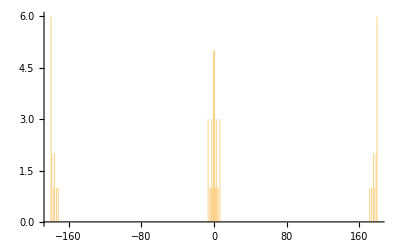

```mathematica
Histogram[MoleculeValue[mol,"TorsionAngle"],360]
```

```mathematica
MoleculeValue[mol,"PubChemCompoundID"]
```

{ExternalIdentifier[PubChemCompoundID,177057]PubChem compound177057https://pubchem.ncbi.nlm.nih.gov/compound/177057}

```mathematica
WordCloud[
 MoleculePlot3D /@ DeleteDuplicates[MoleculeRecognize[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, 
     CloudGet["https://wolfr.am/KR7FBcsM"]}], MoleculeEquivalentQ]]
```

-Graphics-

```mathematica
Import["ExampleData/Pyridinecarbonitrile_MO_25_29.cub","Graphics3D"]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
>[1,2,3+3]
```

[for x in range(10)]

StartExternalSession::noinstall: No valid installations for system Python were found with the options specified.

$Failed

[]

StartExternalSession::noinstall: No valid installations for system NodeJS were found with the options specified.

$Failed

```mathematica
ExternalStoragePut[CloudGet["https://wolfr.am/L9rTMCn6"],ExternalStorageBase->"IPFS"]
```

ExternalStorageObject[…]

```mathematica
%["CID"]
```

QmcijdnK17nnSmxfj2Hbe9VNjEYY5K9gzKjDkoyMCe8FHd

```mathematica
ExternalStorageGet["QmcNotbm3RZLv7caaPasU8LiHjNCCuuEemrCgbLAsN49TZ"]
```

-Graphics3D-

```mathematica
SortedEntityClass[UnionedEntityClass[
    LinguisticAssistant, 
    EntityClass["AdministrativeDivision", "AllUSStatesPlusDC"]], 
   "Population" -> "Descending"][{"Name", "Population"}] // Dataset
```

```mathematica
knee=Import["knee_mr/DICOMDIR",{"Image3D",1,1,1}];
Image3D[knee,ColorFunction->(Blend[{{0.,RGBColor[0.05635,0.081,0.07687,0.]},{0.0777045,RGBColor[0.702347,0.222888,0.0171385,0.0230167]},{0.3,RGBColor[1.,0.6036,0.,0.303215]},{0.66,RGBColor[1.,0.9658,0.4926,0.661561]},{1.,RGBColor[1.,0.6436,0.03622,1.]}},#]&)]//ImageAdjust//Blur[#,3]&
```

Import::nffil: File knee_mr/DICOMDIR not found during Import.

Image3D::imgarray: The specified argument $Failed should be an array of rank 3 or 4 with machine-sized numbers or a list of images of consistent dimension and color space.

ImageAdjust::imginv: Expecting an image or graphics instead of ….

Blur::imginv: Expecting an image or graphics instead of ImageAdjust[Image3D[$Failed,ColorFunction→(Blend[{{0.,RGBColor[«4»]},{0.0777045,RGBColor[«4»]},{0.3,RGBColor[«4»]},{0.66,RGBColor[«4»]},{1.,RGBColor[«4»]}},#1]&)]].

Blur[ImageAdjust[Image3D[$Failed,ColorFunction→(Blend[{{0.,RGBColor[0.05635, 0.081, 0.07687, 0.]},{0.0777045,RGBColor[0.702347, 0.222888, 0.0171385, 0.0230167]},{0.3,RGBColor[1., 0.6036, 0., 0.303215]},{0.66,RGBColor[1., 0.9658, 0.4926, 0.661561]},{1.,RGBColor[1., 0.6436, 0.03622, 1.]}},#1]&)]],3]

```mathematica
knee=Import["knee_mr/DICOMDIR",{"Image3D",1,1,1}]
```

Import::nffil: File knee_mr/DICOMDIR not found during Import.

$Failed

```mathematica
Length[PacletFind[]]
```

250